## Constraint Plots

### Plot the limit

```mathematica
(*Function to convert mass, Log[10,epsilon^{2}]   to   mass, epsilon*)
```

```mathematica
DataConvertermine[data_]:=Table[{data[[i,1]],√(10^data[[i,2]])},{i,Length[data]}]
```

```mathematica
Labelslin={"Br(H->2γ_D)=0.1%","Br(H->2γ_D)=1%","Br(H->2γ_D)=5%","Br(H->2γ_D)=10%","Br(H->2γ_D)=20%","Br(H->2γ_D)=40%"}
```

{Br(H->2γ_D)=0.1%,Br(H->2γ_D)=1%,Br(H->2γ_D)=5%,Br(H->2γ_D)=10%,Br(H->2γ_D)=20%,Br(H->2γ_D)=40%}

```mathematica
DataConvertertest[data_]:=Table[{data[[i,1]],√(10^data[[i,2]])},{i,1,Length[data]}]
```

```mathematica
myopacity=0.5;
```

{{},{0.25,-10.61},{0.3,-10.98},{0.35,-11.21},{0.4,-11.4},{0.45,-11.48},{0.5,-11.54},{0.55,-11.58},{0.6,-11.6},{0.65,-11.58},{0.7,-11.49},{0.7,-11.49},{0.75,-11.43},{0.8,-11.55},{0.85,-11.7},{0.85,-11.7},{0.9,-11.79},{0.95,-11.84},{1.,-11.88},{1.,-11.88},{1.01,-11.86},{1.02,-4.},{1.03,-11.85},{1.04,-11.9},{1.05,-11.91},{1.06,-11.86},{1.07,-11.87},{1.08,-11.88},{1.09,-11.88},{1.1,-11.9},{1.11,-11.91},{1.12,-11.93},{1.13,-11.94},{1.14,-11.96},{1.15,-11.97},{1.16,-11.98},{1.17,-12.},{1.18,-12.02},{1.19,-12.04},{1.2,-12.05},{1.2,-12.05},{1.21,-12.06},{1.22,-12.06},{1.23,-12.08},{1.24,-12.08},{1.25,-12.08},{1.26,-12.1},{1.27,-12.1},{1.28,-12.08},{1.29,-12.03},{1.3,-12.03},{1.31,-12.04},{1.32,-12.04},{1.33,-12.05},{1.34,-12.06},{1.35,-12.1},{1.36,-12.12},{1.37,-12.12},{1.38,-12.14},{1.39,-12.15},{1.4,-12.16},{1.41,-12.18},{1.42,-12.18},{1.43,-12.19},{1.44,-12.19},{1.45,-12.2},{1.46,-12.2},{1.47,-12.2},{1.48,-12.21},{1.49,-12.21},{1.5,-12.22},{1.51,-12.22},{1.52,-12.22},{1.53,-12.24},{1.54,-12.24},{1.55,-12.24},{1.56,-12.24},{1.57,-12.26},{1.58,-12.26},{1.59,-12.26},{1.6,-12.26},{1.61,-12.28},{1.62,-12.28},{1.63,-12.28},{1.64,-12.28},{1.65,-12.28},{1.66,-12.3},{1.67,-12.3},{1.68,-12.3},{1.69,-12.3},{1.7,-12.32},{1.71,-12.32},{1.72,-12.33},{1.73,-12.33},{1.74,-12.33},{1.75,-12.33},{1.76,-12.35},{1.77,-12.36},{1.78,-12.36},{1.79,-12.36},{1.8,-12.38},{1.81,-12.38},{1.82,-12.39},{1.83,-12.39},{1.84,-12.4},{1.85,-12.4},{1.86,-12.4},{1.87,-12.41},{1.88,-12.42},{1.89,-12.42},{1.9,-12.42},{1.91,-12.42},{1.92,-12.44},{1.93,-12.42},{1.94,-12.4},{1.95,-12.36},{1.96,-12.36},{1.97,-12.36},{1.98,-12.36},{1.99,-12.36},{2.,-12.37},{2.,-12.37},{2.01,-12.38},{2.02,-12.4},{2.03,-12.44},{2.04,-12.45},{2.05,-12.45},{2.06,-12.47},{2.07,-12.48},{2.08,-12.48},{2.09,-12.48},{2.1,-12.5},{2.11,-12.5},{2.12,-12.5},{2.13,-12.5},{2.14,-12.51},{2.15,-12.51},{2.16,-12.52},{2.17,-12.52},{2.18,-12.52},{2.19,-12.54},{2.2,-12.54},{2.21,-12.54},{2.22,-12.54},{2.23,-12.56},{2.24,-12.56},{2.25,-12.56},{2.26,-12.56},{2.27,-12.56},{2.28,-12.57},{2.29,-12.57},{2.3,-12.58},{2.31,-12.58},{2.32,-12.58},{2.33,-12.58},{2.34,-12.58},{2.35,-12.58},{2.36,-12.59},{2.37,-12.59},{2.38,-12.6},{2.39,-12.6},{2.4,-12.6},{2.41,-12.56},{2.42,-12.54},{2.43,-12.54},{2.44,-12.54},{2.45,-12.54},{2.46,-12.54},{2.47,-12.55},{2.48,-12.55},{2.49,-12.56},{2.5,-12.57},{2.51,-12.58},{2.52,-12.6},{2.53,-12.6},{2.54,-12.61},{2.55,-12.63},{2.56,-12.64},{2.57,-12.64},{2.58,-12.66},{2.59,-12.66},{2.6,-12.68},{2.61,-12.68},{2.62,-12.69},{2.63,-12.69},{2.64,-12.7},{2.65,-12.7},{2.66,-12.7},{2.67,-12.7},{2.68,-12.7},{2.69,-12.71},{2.7,-12.72},{2.71,-12.72},{2.72,-12.72}}

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

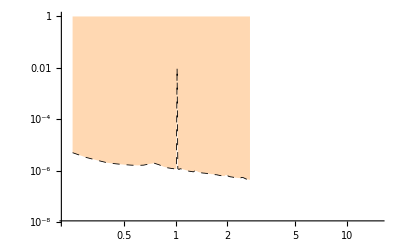

```mathematica
CMS20181part1= Import["/Users/alfre/Documents/GitHub/DarkPhoton_Limits/Limit_epsvsmass_BrHtoGamD_1_2018data_m0to60_observed_part1.dat","Table"]
CMS20181part1plot = ListLogLogPlot[DataConvertertest[CMS20181part1],Joined->True,PlotStyle->{(*Lighter[Orange,0.3]*)Black,Thickness[0.0015],Dashed},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Lighter[Orange,0.4]],PlotRange->{10^-8,1}]
```

{{},{3.24,-12.87},{3.34,-12.9},{3.44,-12.9},{3.54,-12.96},{3.64,-12.96},{3.74,-12.96},{3.84,-13.},{3.94,-13.},{4.04,-13.},{4.14,-13.},{4.24,-13.05},{4.34,-13.05},{4.44,-13.05},{4.54,-13.1},{4.64,-13.1},{4.74,-13.14},{4.84,-13.14},{4.94,-13.1},{5.04,-13.1},{5.14,-13.14},{5.24,-13.2},{5.34,-13.23},{5.44,-13.23},{5.54,-13.23},{5.64,-13.2},{5.74,-13.2},{5.84,-13.28},{5.94,-13.3},{6.04,-13.32},{6.14,-13.36},{6.24,-13.36},{6.34,-13.4},{6.44,-13.4},{6.54,-13.4},{6.64,-13.4},{6.74,-13.44},{6.84,-13.44},{6.94,-13.44},{7.04,-13.5},{7.14,-13.5},{7.24,-13.5},{7.34,-13.5},{7.44,-13.5},{7.54,-13.5},{7.64,-13.52},{7.74,-13.52},{7.84,-13.56},{7.94,-13.59},{8.04,-13.52},{8.14,-13.5},{8.24,-13.44},{8.34,-13.38},{8.44,-13.36},{8.54,-13.4},{8.64,-13.5},{8.74,-13.59},{8.84,-13.52},{8.94,-13.52}}

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

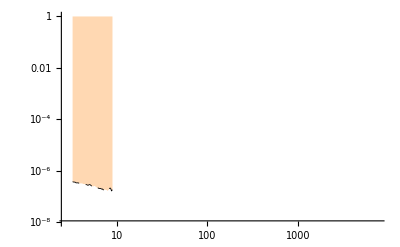

```mathematica
CMS20181part2= Import["/Users/alfre/Documents/GitHub/DarkPhoton_Limits/Limit_epsvsmass_BrHtoGamD_1_2018data_m0to60_observed_part2.dat","Table"]
CMS20181part2plot = ListLogLogPlot[DataConvertertest[CMS20181part2],Joined->True,PlotStyle->{(*Lighter[Orange,0.3]*)Black,Thickness[0.0015],Dashed},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Lighter[Orange,0.4]],PlotRange->{10^-8,1}]
```

{{},{11.,-13.86},{11.1,-13.86},{11.2,-13.86},{11.3,-13.9},{11.4,-13.9},{11.5,-13.9},{11.6,-13.9},{11.7,-13.9},{11.8,-13.9},{11.9,-13.95},{12.,-13.95},{12.1,-13.95},{12.2,-13.95},{12.3,-13.95},{12.4,-13.95},{12.5,-13.95},{12.6,-13.95},{12.7,-13.95},{12.8,-13.95},{12.9,-13.95},{13.,-13.95},{13.1,-13.95},{13.2,-13.95},{13.3,-13.95},{13.4,-14.},{13.5,-14.},{13.6,-14.},{13.7,-14.},{13.8,-14.},{13.9,-14.04},{14.,-14.04},{14.1,-14.04},{14.2,-14.04},{14.3,-14.08},{14.4,-14.1},{14.5,-14.1},{14.6,-14.1},{14.7,-14.1},{14.8,-14.1},{14.9,-14.1},{15.,-14.1},{15.1,-14.1},{15.2,-14.1},{15.3,-14.1},{15.4,-14.1},{15.5,-14.13},{15.6,-14.1},{15.7,-14.1},{15.8,-14.1},{15.9,-14.1},{16.,-14.08},{16.1,-14.1},{16.2,-14.1},{16.3,-14.1},{16.4,-14.1},{16.5,-14.1},{16.6,-14.13},{16.7,-14.13},{16.8,-14.13},{16.9,-14.16},{17.,-14.16},{17.1,-14.16},{17.2,-14.2},{17.3,-14.2},{17.4,-14.2},{17.5,-14.2},{17.6,-14.2},{17.7,-14.22},{17.8,-14.22},{17.9,-14.22},{18.,-14.24},{18.1,-14.24},{18.2,-14.28},{18.3,-14.29},{18.4,-14.3},{18.5,-14.3},{18.6,-14.3},{18.7,-14.3},{18.8,-14.3},{18.9,-14.31},{19.,-14.32},{19.1,-14.32},{19.2,-14.32},{19.3,-14.36},{19.4,-14.36},{19.5,-14.36},{19.6,-14.36},{19.7,-14.36},{19.8,-14.36},{19.9,-14.36},{20.,-14.4},{20.1,-14.4},{20.2,-14.4},{20.3,-14.4},{20.4,-14.4},{20.5,-14.4},{20.6,-14.36},{20.7,-14.36},{20.8,-14.31},{20.9,-14.3},{21.,-14.3},{21.1,-14.28},{21.2,-14.24},{21.3,-14.24},{21.4,-14.22},{21.5,-14.2},{21.6,-14.2},{21.7,-14.19},{21.8,-14.16},{21.9,-14.16},{22.,-14.15},{22.1,-14.16},{22.2,-14.16},{22.3,-14.16},{22.4,-14.16},{22.5,-14.16},{22.6,-14.16},{22.7,-14.16},{22.8,-14.18},{22.9,-14.19},{23.,-14.2},{23.1,-14.2},{23.2,-14.22},{23.3,-14.24},{23.4,-14.24},{23.5,-14.28},{23.6,-14.3},{23.7,-14.3},{23.8,-14.31},{23.9,-14.34},{24.,-14.36},{24.1,-14.37},{24.2,-14.4},{24.3,-14.43},{24.4,-14.43},{24.5,-14.46},{24.6,-14.49},{24.7,-14.5},{24.8,-14.52},{24.9,-14.56},{25.,-14.58},{25.1,-14.58},{25.2,-14.6},{25.3,-14.6},{25.4,-14.6},{25.5,-14.6},{25.6,-14.6},{25.7,-14.64},{25.8,-14.64},{25.9,-14.64},{26.,-14.67},{26.1,-14.67},{26.2,-14.67},{26.3,-14.67},{26.4,-14.7},{26.5,-14.7},{26.6,-14.7},{26.7,-14.7},{26.8,-14.7},{26.9,-14.7},{27.,-14.72},{27.1,-14.72},{27.2,-14.76},{27.3,-14.76},{27.4,-14.76},{27.5,-14.76},{27.6,-14.76},{27.7,-14.76},{27.8,-14.8},{27.9,-14.8},{28.,-14.8},{28.1,-14.8},{28.2,-14.8},{28.3,-14.8},{28.4,-14.8},{28.5,-14.82},{28.6,-14.85},{28.7,-14.85},{28.8,-14.85},{28.9,-14.85},{29.,-14.85},{29.1,-14.85},{29.2,-14.85},{29.3,-14.85},{29.4,-14.88},{29.5,-14.9},{29.6,-14.9},{29.7,-14.9},{29.8,-14.9},{29.9,-14.9},{30.,-14.9},{30.1,-14.9},{30.2,-14.9},{30.3,-14.94},{30.4,-14.94},{30.5,-14.94},{30.6,-14.94},{30.7,-14.94},{30.8,-14.94},{30.9,-14.94},{31.,-14.94},{31.1,-14.96},{31.2,-14.96},{31.3,-14.96},{31.4,-14.96},{31.5,-15.},{31.6,-15.},{31.7,-15.},{31.8,-15.},{31.9,-15.},{32.,-15.},{32.1,-15.},{32.2,-15.},{32.3,-15.},{32.4,-15.},{32.5,-15.03},{32.6,-15.03},{32.7,-15.03},{32.8,-15.03},{32.9,-15.03},{33.,-15.03},{33.1,-15.03},{33.2,-15.04},{33.3,-15.04},{33.4,-15.06},{33.5,-15.06},{33.6,-15.06},{33.7,-15.06},{33.8,-15.1},{33.9,-15.1},{34.,-15.1},{34.1,-15.06},{34.2,-15.04},{34.3,-15.03},{34.4,-15.03},{34.5,-15.03},{34.6,-15.03},{34.7,-15.03},{34.8,-15.03},{34.9,-15.03},{35.,-15.03},{35.1,-15.04},{35.2,-15.06},{35.3,-15.08},{35.4,-15.1},{35.5,-15.1},{35.6,-15.12},{35.7,-15.12},{35.8,-15.13},{35.9,-15.15},{36.,-15.18},{36.1,-15.18},{36.2,-15.2},{36.3,-15.2},{36.4,-15.2},{36.5,-15.2},{36.6,-15.2},{36.7,-15.2},{36.8,-15.21},{36.9,-15.21},{37.,-15.24},{37.1,-15.21},{37.2,-15.21},{37.3,-15.2},{37.4,-15.2},{37.5,-15.2},{37.6,-15.18},{37.7,-15.13},{37.8,-15.12},{37.9,-15.1},{38.,-15.06},{38.1,-15.06},{38.2,-15.06},{38.3,-15.05},{38.4,-15.04},{38.5,-15.03},{38.6,-15.04},{38.7,-15.06},{38.8,-15.06},{38.9,-15.08},{39.,-15.08},{39.1,-15.08},{39.2,-15.07},{39.3,-15.06},{39.4,-15.06},{39.5,-15.05},{39.6,-15.06},{39.7,-15.08},{39.8,-15.09},{39.9,-15.1},{40.,-15.12},{40.1,-15.12},{40.2,-15.12},{40.3,-15.12},{40.4,-15.12},{40.5,-15.12},{40.6,-15.12},{40.7,-15.13},{40.8,-15.13},{40.9,-15.15},{41.,-15.15},{41.1,-15.15},{41.2,-15.16},{41.3,-15.18},{41.4,-15.18},{41.5,-15.19},{41.6,-15.2},{41.7,-15.22},{41.8,-15.24},{41.9,-15.25},{42.,-15.28},{42.1,-15.3},{42.2,-15.32},{42.3,-15.34},{42.4,-15.36},{42.5,-15.36},{42.6,-15.4},{42.7,-15.4},{42.8,-15.44},{42.9,-15.44},{43.,-15.5},{43.1,-15.5},{43.2,-15.5},{43.3,-15.5},{43.4,-15.5},{43.5,-15.5},{43.6,-15.5},{43.7,-15.5},{43.8,-15.5},{43.9,-15.52},{44.,-15.52},{44.1,-15.52},{44.2,-15.52},{44.3,-15.55},{44.4,-15.55},{44.5,-15.57},{44.6,-15.57},{44.7,-15.57},{44.8,-15.57},{44.9,-15.57},{45.,-15.57},{45.1,-15.57},{45.2,-15.57},{45.3,-15.6},{45.4,-15.6},{45.5,-15.6},{45.6,-15.6},{45.7,-15.6},{45.8,-15.6},{45.9,-15.6},{46.,-15.6},{46.1,-15.6},{46.2,-15.6},{46.3,-15.6},{46.4,-15.6},{46.5,-15.62},{46.6,-15.62},{46.7,-15.62},{46.8,-15.62},{46.9,-15.62},{47.,-15.62},{47.1,-15.62},{47.2,-15.62},{47.3,-15.62},{47.4,-15.62},{47.5,-15.62},{47.6,-15.6},{47.7,-15.6},{47.8,-15.57},{47.9,-15.55},{48.,-15.55},{48.1,-15.54},{48.2,-15.54},{48.3,-15.52},{48.4,-15.52},{48.5,-15.52},{48.6,-15.52},{48.7,-15.54},{48.8,-15.55},{48.9,-15.55},{49.,-15.55},{49.1,-15.57},{49.2,-15.57},{49.3,-15.6},{49.4,-15.6},{49.5,-15.62},{49.6,-15.62},{49.7,-15.66},{49.8,-15.66},{49.9,-15.66},{50.,-15.7},{50.1,-15.7},{50.2,-15.68},{50.3,-15.66},{50.4,-15.66},{50.5,-15.66},{50.6,-15.66},{50.7,-15.66},{50.8,-15.66},{50.9,-15.66},{51.,-15.66},{51.1,-15.68},{51.2,-15.68},{51.3,-15.68},{51.4,-15.7},{51.5,-15.7},{51.6,-15.7},{51.7,-15.7},{51.8,-15.72},{51.9,-15.72},{52.,-15.75},{52.1,-15.75},{52.2,-15.75},{52.3,-15.75},{52.4,-15.75},{52.5,-15.76},{52.6,-15.76},{52.7,-15.8},{52.8,-15.8},{52.9,-15.8},{53.,-15.8},{53.1,-15.8},{53.2,-15.8},{53.3,-15.8},{53.4,-15.8},{53.5,-15.8},{53.6,-15.8},{53.7,-15.76},{53.8,-15.75},{53.9,-15.75},{54.,-15.75},{54.1,-15.75},{54.2,-15.75},{54.3,-15.75},{54.4,-15.75},{54.5,-15.75},{54.6,-15.75},{54.7,-15.76},{54.8,-15.76},{54.9,-15.78},{55.,-15.78},{55.1,-15.8},{55.2,-15.8},{55.3,-15.8},{55.4,-15.8},{55.5,-15.84},{55.6,-15.84},{55.7,-15.84},{55.8,-15.84},{55.9,-15.84},{56.,-15.84},{56.1,-15.84},{56.2,-15.84},{56.3,-15.84},{56.4,-15.84},{56.5,-15.84},{56.6,-15.84},{56.7,-15.84},{56.8,-15.84},{56.9,-15.84},{57.,-15.84},{57.1,-15.84},{57.2,-15.84},{57.3,-15.85},{57.4,-15.85},{57.5,-15.88},{57.6,-15.85},{57.7,-15.84},{57.8,-15.84},{57.9,-15.84},{58.,-15.84},{58.1,-15.84},{58.2,-15.84},{58.3,-15.84},{58.4,-15.84},{58.5,-15.84},{58.6,-15.84},{58.7,-15.84},{58.8,-15.84},{58.9,-15.85},{59.,-15.85},{59.1,-15.85},{59.2,-15.88},{59.3,-15.88},{59.4,-15.88},{59.5,-15.88},{59.6,-15.9},{59.7,-15.9},{59.8,-15.9},{59.9,-15.9},{60.,-15.9}}

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

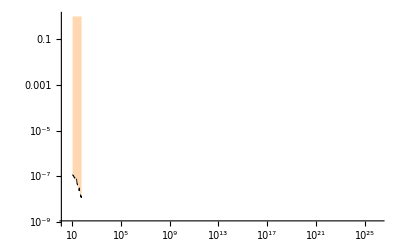

```mathematica
CMS20181part3= Import["/Users/alfre/Documents/GitHub/DarkPhoton_Limits/Limit_epsvsmass_BrHtoGamD_1_2018data_m0to60_observed_part3.dat","Table"]
CMS20181part3plot = ListLogLogPlot[DataConvertertest[CMS20181part3],Joined->True,PlotStyle->{(*Lighter[Orange,0.3]*)Black,Thickness[0.0015],Dashed},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Lighter[Orange,0.4]],PlotRange->{10^-9,1}]
```

{{},{0.25,-11.12},{0.35,-11.72},{0.45,-12.},{0.55,-12.1},{0.65,-12.12},{0.7,-12.1},{0.8,-12.2},{0.85,-12.26},{0.95,-12.39},{1.,-12.42},{1.05,-12.45},{1.1,-12.45},{1.15,-12.5},{1.2,-12.57},{1.2,-12.57},{1.25,-12.61},{1.3,-12.57},{1.35,-12.64},{1.4,-12.7},{1.45,-12.75},{1.5,-12.78},{1.55,-12.8},{1.6,-12.82},{1.65,-12.84},{1.7,-12.87},{1.75,-12.9},{1.8,-12.92},{1.85,-12.96},{1.9,-12.96},{1.95,-12.92},{2.,-12.95},{2.,-12.95},{2.05,-13.},{2.1,-13.05},{2.15,-13.08},{2.2,-13.1},{2.25,-13.1},{2.3,-13.14},{2.35,-13.14},{2.4,-13.14},{2.45,-13.1},{2.5,-13.14},{2.55,-13.2},{2.6,-13.23},{2.65,-13.24},{2.7,-13.28}}

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

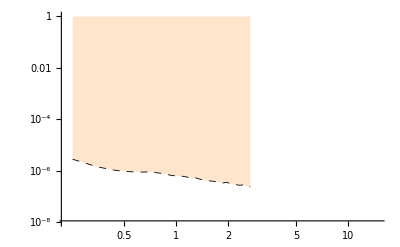

```mathematica
CMS201810part1= Import["/Users/alfre/Documents/GitHub/DarkPhoton_Limits/Limit_epsvsmass_BrHtoGamD_10_2018data_m0to60_observed_part1.dat","Table"]
CMS201810part1plot = ListLogLogPlot[DataConvertertest[CMS201810part1],Joined->True,PlotStyle->{(*Lighter[Orange,0.3]*)Black,Thickness[0.0015],Dashed},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Lighter[Orange,0.6]],PlotRange->{10^-8,1}]
```

{{},{3.24,-13.44},{3.34,-13.44},{3.44,-13.5},{3.54,-13.5},{3.64,-13.52},{3.74,-13.56},{3.84,-13.59},{3.94,-13.6},{4.04,-13.6},{4.14,-13.62},{4.24,-13.66},{4.34,-13.68},{4.44,-13.7},{4.54,-13.7},{4.64,-13.73},{4.74,-13.76},{4.84,-13.77},{4.94,-13.73},{5.04,-13.73},{5.14,-13.77},{5.24,-13.8},{5.34,-13.84},{5.44,-13.86},{5.54,-13.86},{5.64,-13.84},{5.74,-13.84},{5.84,-13.9},{5.94,-13.92},{6.04,-13.95},{6.14,-13.95},{6.24,-13.98},{6.34,-14.},{6.44,-14.},{6.54,-14.04},{6.64,-14.04},{6.74,-14.04},{6.84,-14.08},{6.94,-14.08},{7.04,-14.1},{7.14,-14.1},{7.24,-14.1},{7.34,-14.13},{7.44,-14.13},{7.54,-14.13},{7.64,-14.16},{7.74,-14.16},{7.84,-14.16},{7.94,-14.2},{8.04,-14.16},{8.14,-14.13},{8.24,-14.1},{8.34,-14.05},{8.44,-14.05},{8.54,-14.1},{8.64,-14.16},{8.74,-14.2},{8.84,-14.18},{8.94,-14.19}}

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

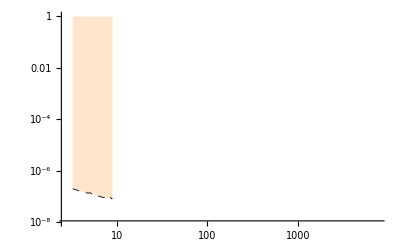

```mathematica
CMS201810part2= Import["/Users/alfre/Documents/GitHub/DarkPhoton_Limits/Limit_epsvsmass_BrHtoGamD_10_2018data_m0to60_observed_part2.dat","Table"]
CMS201810part2plot = ListLogLogPlot[DataConvertertest[CMS201810part2],Joined->True,PlotStyle->{(*Lighter[Orange,0.3]*)Black,Thickness[0.0015],Dashed},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Lighter[Orange,0.6]],PlotRange->{10^-8,1}]
```

{{},{11.,-14.48},{11.1,-14.49},{11.2,-14.5},{11.3,-14.5},{11.4,-14.5},{11.5,-14.5},{11.6,-14.5},{11.7,-14.52},{11.8,-14.52},{11.9,-14.52},{12.,-14.56},{12.1,-14.56},{12.2,-14.56},{12.3,-14.58},{12.4,-14.58},{12.5,-14.58},{12.6,-14.58},{12.7,-14.6},{12.8,-14.6},{12.9,-14.6},{13.,-14.6},{13.1,-14.6},{13.2,-14.6},{13.3,-14.64},{13.4,-14.64},{13.5,-14.64},{13.6,-14.64},{13.7,-14.67},{13.8,-14.67},{13.9,-14.67},{14.,-14.67},{14.1,-14.67},{14.2,-14.7},{14.3,-14.7},{14.4,-14.7},{14.5,-14.7},{14.6,-14.7},{14.7,-14.7},{14.8,-14.72},{14.9,-14.72},{15.,-14.72},{15.1,-14.72},{15.2,-14.72},{15.3,-14.75},{15.4,-14.76},{15.5,-14.76},{15.6,-14.75},{15.7,-14.72},{15.8,-14.72},{15.9,-14.72},{16.,-14.72},{16.1,-14.72},{16.2,-14.72},{16.3,-14.75},{16.4,-14.75},{16.5,-14.76},{16.6,-14.76},{16.7,-14.76},{16.8,-14.76},{16.9,-14.78},{17.,-14.8},{17.1,-14.8},{17.2,-14.8},{17.3,-14.8},{17.4,-14.82},{17.5,-14.82},{17.6,-14.85},{17.7,-14.85},{17.8,-14.85},{17.9,-14.85},{18.,-14.88},{18.1,-14.88},{18.2,-14.88},{18.3,-14.9},{18.4,-14.9},{18.5,-14.9},{18.6,-14.9},{18.7,-14.92},{18.8,-14.94},{18.9,-14.94},{19.,-14.94},{19.1,-14.94},{19.2,-14.94},{19.3,-14.96},{19.4,-14.96},{19.5,-14.96},{19.6,-14.96},{19.7,-14.99},{19.8,-15.},{19.9,-15.},{20.,-15.},{20.1,-15.},{20.2,-15.},{20.3,-15.},{20.4,-15.},{20.5,-15.},{20.6,-15.},{20.7,-14.99},{20.8,-14.96},{20.9,-14.94},{21.,-14.94},{21.1,-14.94},{21.2,-14.92},{21.3,-14.92},{21.4,-14.9},{21.5,-14.9},{21.6,-14.88},{21.7,-14.88},{21.8,-14.88},{21.9,-14.88},{22.,-14.87},{22.1,-14.87},{22.2,-14.88},{22.3,-14.88},{22.4,-14.88},{22.5,-14.88},{22.6,-14.89},{22.7,-14.9},{22.8,-14.9},{22.9,-14.9},{23.,-14.91},{23.1,-14.92},{23.2,-14.94},{23.3,-14.94},{23.4,-14.96},{23.5,-14.96},{23.6,-14.99},{23.7,-15.},{23.8,-15.},{23.9,-15.03},{24.,-15.03},{24.1,-15.04},{24.2,-15.06},{24.3,-15.08},{24.4,-15.1},{24.5,-15.1},{24.6,-15.12},{24.7,-15.13},{24.8,-15.15},{24.9,-15.18},{25.,-15.2},{25.1,-15.2},{25.2,-15.2},{25.3,-15.2},{25.4,-15.21},{25.5,-15.21},{25.6,-15.24},{25.7,-15.24},{25.8,-15.24},{25.9,-15.27},{26.,-15.27},{26.1,-15.28},{26.2,-15.28},{26.3,-15.28},{26.4,-15.3},{26.5,-15.3},{26.6,-15.3},{26.7,-15.3},{26.8,-15.3},{26.9,-15.34},{27.,-15.34},{27.1,-15.34},{27.2,-15.34},{27.3,-15.36},{27.4,-15.36},{27.5,-15.36},{27.6,-15.36},{27.7,-15.36},{27.8,-15.39},{27.9,-15.39},{28.,-15.4},{28.1,-15.4},{28.2,-15.4},{28.3,-15.4},{28.4,-15.4},{28.5,-15.4},{28.6,-15.41},{28.7,-15.44},{28.8,-15.44},{28.9,-15.44},{29.,-15.44},{29.1,-15.44},{29.2,-15.44},{29.3,-15.44},{29.4,-15.45},{29.5,-15.48},{29.6,-15.48},{29.7,-15.48},{29.8,-15.48},{29.9,-15.5},{30.,-15.5},{30.1,-15.5},{30.2,-15.5},{30.3,-15.5},{30.4,-15.5},{30.5,-15.5},{30.6,-15.5},{30.7,-15.52},{30.8,-15.52},{30.9,-15.52},{31.,-15.52},{31.1,-15.55},{31.2,-15.55},{31.3,-15.55},{31.4,-15.57},{31.5,-15.57},{31.6,-15.57},{31.7,-15.57},{31.8,-15.57},{31.9,-15.57},{32.,-15.57},{32.1,-15.6},{32.2,-15.6},{32.3,-15.6},{32.4,-15.6},{32.5,-15.6},{32.6,-15.6},{32.7,-15.6},{32.8,-15.6},{32.9,-15.6},{33.,-15.62},{33.1,-15.62},{33.2,-15.62},{33.3,-15.62},{33.4,-15.62},{33.5,-15.65},{33.6,-15.66},{33.7,-15.66},{33.8,-15.66},{33.9,-15.66},{34.,-15.66},{34.1,-15.66},{34.2,-15.62},{34.3,-15.62},{34.4,-15.6},{34.5,-15.6},{34.6,-15.6},{34.7,-15.6},{34.8,-15.62},{34.9,-15.62},{35.,-15.62},{35.1,-15.62},{35.2,-15.65},{35.3,-15.66},{35.4,-15.66},{35.5,-15.68},{35.6,-15.7},{35.7,-15.7},{35.8,-15.7},{35.9,-15.72},{36.,-15.75},{36.1,-15.75},{36.2,-15.75},{36.3,-15.75},{36.4,-15.75},{36.5,-15.76},{36.6,-15.76},{36.7,-15.78},{36.8,-15.8},{36.9,-15.8},{37.,-15.8},{37.1,-15.8},{37.2,-15.78},{37.3,-15.78},{37.4,-15.76},{37.5,-15.76},{37.6,-15.75},{37.7,-15.72},{37.8,-15.7},{37.9,-15.68},{38.,-15.66},{38.1,-15.66},{38.2,-15.65},{38.3,-15.65},{38.4,-15.64},{38.5,-15.64},{38.6,-15.65},{38.7,-15.66},{38.8,-15.66},{38.9,-15.67},{39.,-15.68},{39.1,-15.68},{39.2,-15.67},{39.3,-15.66},{39.4,-15.66},{39.5,-15.65},{39.6,-15.66},{39.7,-15.68},{39.8,-15.68},{39.9,-15.7},{40.,-15.71},{40.1,-15.71},{40.2,-15.71},{40.3,-15.71},{40.4,-15.71},{40.5,-15.71},{40.6,-15.72},{40.7,-15.72},{40.8,-15.73},{40.9,-15.73},{41.,-15.74},{41.1,-15.75},{41.2,-15.75},{41.3,-15.76},{41.4,-15.76},{41.5,-15.78},{41.6,-15.79},{41.7,-15.8},{41.8,-15.81},{41.9,-15.83},{42.,-15.84},{42.1,-15.87},{42.2,-15.88},{42.3,-15.9},{42.4,-15.9},{42.5,-15.93},{42.6,-15.95},{42.7,-15.97},{42.8,-15.99},{42.9,-16.},{43.,-16.02},{43.1,-16.02},{43.2,-16.04},{43.3,-16.04},{43.4,-16.04},{43.5,-16.04},{43.6,-16.04},{43.7,-16.05},{43.8,-16.08},{43.9,-16.08},{44.,-16.08},{44.1,-16.08},{44.2,-16.08},{44.3,-16.1},{44.4,-16.1},{44.5,-16.1},{44.6,-16.1},{44.7,-16.1},{44.8,-16.1},{44.9,-16.1},{45.,-16.1},{45.1,-16.1},{45.2,-16.11},{45.3,-16.11},{45.4,-16.11},{45.5,-16.14},{45.6,-16.14},{45.7,-16.14},{45.8,-16.14},{45.9,-16.16},{46.,-16.16},{46.1,-16.16},{46.2,-16.16},{46.3,-16.16},{46.4,-16.16},{46.5,-16.16},{46.6,-16.16},{46.7,-16.16},{46.8,-16.16},{46.9,-16.16},{47.,-16.18},{47.1,-16.16},{47.2,-16.16},{47.3,-16.16},{47.4,-16.16},{47.5,-16.16},{47.6,-16.16},{47.7,-16.14},{47.8,-16.11},{47.9,-16.1},{48.,-16.1},{48.1,-16.1},{48.2,-16.08},{48.3,-16.08},{48.4,-16.08},{48.5,-16.08},{48.6,-16.08},{48.7,-16.1},{48.8,-16.1},{48.9,-16.1},{49.,-16.1},{49.1,-16.11},{49.2,-16.14},{49.3,-16.14},{49.4,-16.16},{49.5,-16.16},{49.6,-16.18},{49.7,-16.2},{49.8,-16.2},{49.9,-16.23},{50.,-16.24},{50.1,-16.24},{50.2,-16.23},{50.3,-16.23},{50.4,-16.2},{50.5,-16.2},{50.6,-16.2},{50.7,-16.2},{50.8,-16.2},{50.9,-16.22},{51.,-16.23},{51.1,-16.23},{51.2,-16.23},{51.3,-16.24},{51.4,-16.24},{51.5,-16.24},{51.6,-16.24},{51.7,-16.25},{51.8,-16.25},{51.9,-16.26},{52.,-16.29},{52.1,-16.3},{52.2,-16.3},{52.3,-16.3},{52.4,-16.3},{52.5,-16.3},{52.6,-16.3},{52.7,-16.32},{52.8,-16.32},{52.9,-16.32},{53.,-16.32},{53.1,-16.32},{53.2,-16.32},{53.3,-16.32},{53.4,-16.32},{53.5,-16.32},{53.6,-16.32},{53.7,-16.32},{53.8,-16.3},{53.9,-16.3},{54.,-16.3},{54.1,-16.3},{54.2,-16.3},{54.3,-16.3},{54.4,-16.3},{54.5,-16.3},{54.6,-16.3},{54.7,-16.3},{54.8,-16.32},{54.9,-16.32},{55.,-16.32},{55.1,-16.32},{55.2,-16.35},{55.3,-16.35},{55.4,-16.35},{55.5,-16.38},{55.6,-16.38},{55.7,-16.38},{55.8,-16.38},{55.9,-16.38},{56.,-16.4},{56.1,-16.38},{56.2,-16.38},{56.3,-16.38},{56.4,-16.38},{56.5,-16.38},{56.6,-16.38},{56.7,-16.38},{56.8,-16.38},{56.9,-16.38},{57.,-16.38},{57.1,-16.4},{57.2,-16.4},{57.3,-16.4},{57.4,-16.4},{57.5,-16.4},{57.6,-16.4},{57.7,-16.4},{57.8,-16.38},{57.9,-16.38},{58.,-16.38},{58.1,-16.38},{58.2,-16.38},{58.3,-16.38},{58.4,-16.38},{58.5,-16.38},{58.6,-16.4},{58.7,-16.4},{58.8,-16.4},{58.9,-16.4},{59.,-16.4},{59.1,-16.4},{59.2,-16.41},{59.3,-16.41},{59.4,-16.41},{59.5,-16.42},{59.6,-16.44},{59.7,-16.44},{59.8,-16.44},{59.9,-16.44},{60.,-16.44}}

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

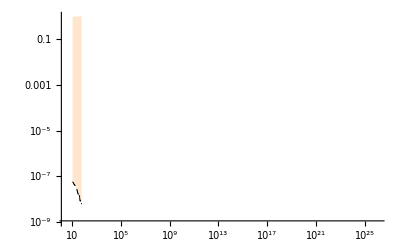

```mathematica
CMS201810part3= Import["/Users/alfre/Documents/GitHub/DarkPhoton_Limits/Limit_epsvsmass_BrHtoGamD_10_2018data_m0to60_observed_part3.dat","Table"]
CMS201810part3plot = ListLogLogPlot[DataConvertertest[CMS201810part3],Joined->True,PlotStyle->{(*Lighter[Orange,0.3]*)Black,Thickness[0.0015],Dashed},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Lighter[Orange,0.6]],PlotRange->{10^-9,1}]
```

{{},{0.25,-11.36},{0.35,-11.97},{0.45,-12.24},{0.55,-12.33},{0.65,-12.36},{0.7,-12.33},{0.8,-12.47},{0.85,-12.51},{0.95,-12.64},{1.,-12.69},{1.05,-12.7},{1.1,-12.69},{1.15,-12.75},{1.2,-12.82},{1.2,-12.82},{1.25,-12.87},{1.3,-12.82},{1.35,-12.9},{1.4,-12.96},{1.45,-13.},{1.5,-13.03},{1.55,-13.05},{1.6,-13.08},{1.65,-13.1},{1.7,-13.14},{1.75,-13.14},{1.8,-13.17},{1.85,-13.2},{1.9,-13.23},{1.95,-13.17},{2.,-13.2},{2.,-13.2},{2.05,-13.28},{2.1,-13.3},{2.15,-13.32},{2.2,-13.36},{2.25,-13.36},{2.3,-13.4},{2.35,-13.4},{2.4,-13.4},{2.45,-13.36},{2.5,-13.4},{2.55,-13.44},{2.6,-13.5},{2.65,-13.5},{2.7,-13.52}}

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

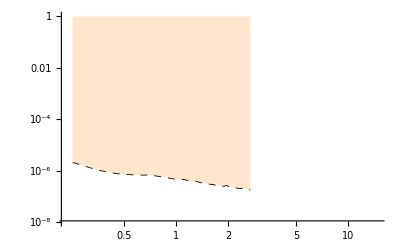

```mathematica
CMS201830part1= Import["/Users/alfre/Documents/GitHub/DarkPhoton_Limits/Limit_epsvsmass_BrHtoGamD_30_2018data_m0to60_observed_part1.dat","Table"]
CMS201830part1plot = ListLogLogPlot[DataConvertertest[CMS201830part1],Joined->True,PlotStyle->{(*Lighter[Orange,0.3]*)Black,Thickness[0.0015],Dashed},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Lighter[Orange,0.6]],PlotRange->{10^-8,1}]
```

{{},{3.24,-13.68},{3.34,-13.7},{3.44,-13.73},{3.54,-13.77},{3.64,-13.77},{3.74,-13.8},{3.84,-13.84},{3.94,-13.86},{4.04,-13.86},{4.14,-13.9},{4.24,-13.9},{4.34,-13.92},{4.44,-13.95},{4.54,-13.95},{4.64,-14.},{4.74,-14.},{4.84,-14.},{4.94,-14.},{5.04,-14.},{5.14,-14.04},{5.24,-14.08},{5.34,-14.1},{5.44,-14.1},{5.54,-14.13},{5.64,-14.1},{5.74,-14.1},{5.84,-14.16},{5.94,-14.2},{6.04,-14.2},{6.14,-14.22},{6.24,-14.22},{6.34,-14.24},{6.44,-14.28},{6.54,-14.29},{6.64,-14.3},{6.74,-14.3},{6.84,-14.3},{6.94,-14.32},{7.04,-14.36},{7.14,-14.36},{7.24,-14.36},{7.34,-14.36},{7.44,-14.4},{7.54,-14.4},{7.64,-14.4},{7.74,-14.43},{7.84,-14.43},{7.94,-14.43},{8.04,-14.43},{8.14,-14.4},{8.24,-14.37},{8.34,-14.32},{8.44,-14.32},{8.54,-14.36},{8.64,-14.43},{8.74,-14.46},{8.84,-14.43},{8.94,-14.45}}

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

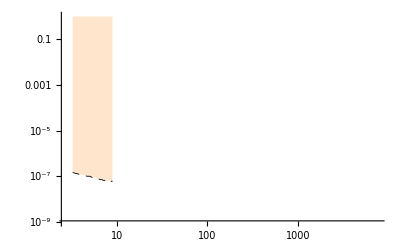

```mathematica
CMS201830part2= Import["/Users/alfre/Documents/GitHub/DarkPhoton_Limits/Limit_epsvsmass_BrHtoGamD_30_2018data_m0to60_observed_part2.dat","Table"]
CMS201830part2plot = ListLogLogPlot[DataConvertertest[CMS201830part2],Joined->True,PlotStyle->{(*Lighter[Orange,0.3]*)Black,Thickness[0.0015],Dashed},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Lighter[Orange,0.6]],PlotRange->{10^-9,1}]
```

{{},{11.,-14.72},{11.1,-14.72},{11.2,-14.76},{11.3,-14.76},{11.4,-14.76},{11.5,-14.76},{11.6,-14.76},{11.7,-14.8},{11.8,-14.8},{11.9,-14.8},{12.,-14.8},{12.1,-14.8},{12.2,-14.8},{12.3,-14.82},{12.4,-14.82},{12.5,-14.85},{12.6,-14.85},{12.7,-14.85},{12.8,-14.85},{12.9,-14.85},{13.,-14.85},{13.1,-14.88},{13.2,-14.88},{13.3,-14.9},{13.4,-14.9},{13.5,-14.9},{13.6,-14.9},{13.7,-14.9},{13.8,-14.9},{13.9,-14.94},{14.,-14.94},{14.1,-14.94},{14.2,-14.94},{14.3,-14.94},{14.4,-14.94},{14.5,-14.96},{14.6,-14.96},{14.7,-14.96},{14.8,-14.99},{14.9,-15.},{15.,-15.},{15.1,-15.},{15.2,-15.},{15.3,-15.},{15.4,-15.},{15.5,-15.},{15.6,-15.},{15.7,-15.},{15.8,-15.},{15.9,-14.99},{16.,-14.99},{16.1,-14.99},{16.2,-15.},{16.3,-15.},{16.4,-15.},{16.5,-15.},{16.6,-15.03},{16.7,-15.03},{16.8,-15.03},{16.9,-15.03},{17.,-15.04},{17.1,-15.06},{17.2,-15.06},{17.3,-15.06},{17.4,-15.08},{17.5,-15.1},{17.6,-15.1},{17.7,-15.1},{17.8,-15.1},{17.9,-15.12},{18.,-15.12},{18.1,-15.12},{18.2,-15.13},{18.3,-15.15},{18.4,-15.15},{18.5,-15.18},{18.6,-15.18},{18.7,-15.18},{18.8,-15.2},{18.9,-15.2},{19.,-15.2},{19.1,-15.2},{19.2,-15.2},{19.3,-15.2},{19.4,-15.21},{19.5,-15.21},{19.6,-15.24},{19.7,-15.24},{19.8,-15.24},{19.9,-15.24},{20.,-15.24},{20.1,-15.27},{20.2,-15.27},{20.3,-15.28},{20.4,-15.28},{20.5,-15.28},{20.6,-15.27},{20.7,-15.24},{20.8,-15.24},{20.9,-15.21},{21.,-15.2},{21.1,-15.2},{21.2,-15.18},{21.3,-15.18},{21.4,-15.16},{21.5,-15.16},{21.6,-15.15},{21.7,-15.15},{21.8,-15.15},{21.9,-15.15},{22.,-15.14},{22.1,-15.14},{22.2,-15.15},{22.3,-15.15},{22.4,-15.15},{22.5,-15.15},{22.6,-15.16},{22.7,-15.16},{22.8,-15.17},{22.9,-15.18},{23.,-15.18},{23.1,-15.19},{23.2,-15.2},{23.3,-15.21},{23.4,-15.22},{23.5,-15.24},{23.6,-15.24},{23.7,-15.26},{23.8,-15.28},{23.9,-15.28},{24.,-15.3},{24.1,-15.32},{24.2,-15.32},{24.3,-15.34},{24.4,-15.36},{24.5,-15.36},{24.6,-15.39},{24.7,-15.4},{24.8,-15.4},{24.9,-15.44},{25.,-15.44},{25.1,-15.44},{25.2,-15.45},{25.3,-15.48},{25.4,-15.48},{25.5,-15.5},{25.6,-15.5},{25.7,-15.5},{25.8,-15.5},{25.9,-15.5},{26.,-15.52},{26.1,-15.52},{26.2,-15.52},{26.3,-15.55},{26.4,-15.55},{26.5,-15.55},{26.6,-15.57},{26.7,-15.57},{26.8,-15.57},{26.9,-15.57},{27.,-15.6},{27.1,-15.6},{27.2,-15.6},{27.3,-15.6},{27.4,-15.6},{27.5,-15.6},{27.6,-15.62},{27.7,-15.62},{27.8,-15.62},{27.9,-15.62},{28.,-15.65},{28.1,-15.66},{28.2,-15.66},{28.3,-15.66},{28.4,-15.66},{28.5,-15.66},{28.6,-15.66},{28.7,-15.68},{28.8,-15.7},{28.9,-15.7},{29.,-15.7},{29.1,-15.7},{29.2,-15.7},{29.3,-15.7},{29.4,-15.7},{29.5,-15.72},{29.6,-15.72},{29.7,-15.72},{29.8,-15.75},{29.9,-15.75},{30.,-15.75},{30.1,-15.75},{30.2,-15.75},{30.3,-15.75},{30.4,-15.75},{30.5,-15.75},{30.6,-15.76},{30.7,-15.76},{30.8,-15.78},{30.9,-15.8},{31.,-15.8},{31.1,-15.8},{31.2,-15.8},{31.3,-15.8},{31.4,-15.8},{31.5,-15.8},{31.6,-15.8},{31.7,-15.83},{31.8,-15.84},{31.9,-15.84},{32.,-15.84},{32.1,-15.84},{32.2,-15.84},{32.3,-15.84},{32.4,-15.84},{32.5,-15.84},{32.6,-15.84},{32.7,-15.85},{32.8,-15.85},{32.9,-15.88},{33.,-15.88},{33.1,-15.88},{33.2,-15.88},{33.3,-15.9},{33.4,-15.9},{33.5,-15.9},{33.6,-15.9},{33.7,-15.9},{33.8,-15.9},{33.9,-15.9},{34.,-15.9},{34.1,-15.9},{34.2,-15.9},{34.3,-15.88},{34.4,-15.88},{34.5,-15.85},{34.6,-15.85},{34.7,-15.87},{34.8,-15.88},{34.9,-15.88},{35.,-15.88},{35.1,-15.88},{35.2,-15.9},{35.3,-15.9},{35.4,-15.93},{35.5,-15.93},{35.6,-15.93},{35.7,-15.97},{35.8,-15.97},{35.9,-15.97},{36.,-16.},{36.1,-16.},{36.2,-16.},{36.3,-16.},{36.4,-16.},{36.5,-16.02},{36.6,-16.02},{36.7,-16.02},{36.8,-16.02},{36.9,-16.04},{37.,-16.04},{37.1,-16.02},{37.2,-16.02},{37.3,-16.02},{37.4,-16.02},{37.5,-16.02},{37.6,-16.},{37.7,-15.97},{37.8,-15.95},{37.9,-15.93},{38.,-15.92},{38.1,-15.91},{38.2,-15.9},{38.3,-15.9},{38.4,-15.9},{38.5,-15.89},{38.6,-15.9},{38.7,-15.91},{38.8,-15.92},{38.9,-15.93},{39.,-15.93},{39.1,-15.93},{39.2,-15.92},{39.3,-15.92},{39.4,-15.91},{39.5,-15.91},{39.6,-15.92},{39.7,-15.93},{39.8,-15.94},{39.9,-15.95},{40.,-15.97},{40.1,-15.97},{40.2,-15.97},{40.3,-15.97},{40.4,-15.97},{40.5,-15.97},{40.6,-15.97},{40.7,-15.98},{40.8,-15.98},{40.9,-15.99},{41.,-15.99},{41.1,-16.},{41.2,-16.},{41.3,-16.02},{41.4,-16.02},{41.5,-16.03},{41.6,-16.04},{41.7,-16.05},{41.8,-16.07},{41.9,-16.08},{42.,-16.1},{42.1,-16.11},{42.2,-16.12},{42.3,-16.14},{42.4,-16.16},{42.5,-16.18},{42.6,-16.2},{42.7,-16.22},{42.8,-16.24},{42.9,-16.24},{43.,-16.29},{43.1,-16.29},{43.2,-16.3},{43.3,-16.3},{43.4,-16.3},{43.5,-16.3},{43.6,-16.3},{43.7,-16.3},{43.8,-16.3},{43.9,-16.3},{44.,-16.32},{44.1,-16.32},{44.2,-16.32},{44.3,-16.32},{44.4,-16.32},{44.5,-16.35},{44.6,-16.35},{44.7,-16.35},{44.8,-16.35},{44.9,-16.35},{45.,-16.35},{45.1,-16.38},{45.2,-16.38},{45.3,-16.38},{45.4,-16.38},{45.5,-16.38},{45.6,-16.38},{45.7,-16.4},{45.8,-16.4},{45.9,-16.4},{46.,-16.4},{46.1,-16.4},{46.2,-16.4},{46.3,-16.4},{46.4,-16.4},{46.5,-16.4},{46.6,-16.4},{46.7,-16.4},{46.8,-16.41},{46.9,-16.41},{47.,-16.44},{47.1,-16.44},{47.2,-16.41},{47.3,-16.41},{47.4,-16.41},{47.5,-16.41},{47.6,-16.4},{47.7,-16.38},{47.8,-16.38},{47.9,-16.35},{48.,-16.35},{48.1,-16.35},{48.2,-16.34},{48.3,-16.34},{48.4,-16.34},{48.5,-16.34},{48.6,-16.34},{48.7,-16.35},{48.8,-16.35},{48.9,-16.35},{49.,-16.35},{49.1,-16.36},{49.2,-16.38},{49.3,-16.4},{49.4,-16.4},{49.5,-16.41},{49.6,-16.44},{49.7,-16.44},{49.8,-16.46},{49.9,-16.47},{50.,-16.47},{50.1,-16.47},{50.2,-16.47},{50.3,-16.47},{50.4,-16.47},{50.5,-16.46},{50.6,-16.46},{50.7,-16.47},{50.8,-16.47},{50.9,-16.47},{51.,-16.47},{51.1,-16.47},{51.2,-16.47},{51.3,-16.47},{51.4,-16.47},{51.5,-16.48},{51.6,-16.5},{51.7,-16.5},{51.8,-16.5},{51.9,-16.53},{52.,-16.53},{52.1,-16.53},{52.2,-16.53},{52.3,-16.56},{52.4,-16.56},{52.5,-16.56},{52.6,-16.56},{52.7,-16.56},{52.8,-16.56},{52.9,-16.56},{53.,-16.59},{53.1,-16.59},{53.2,-16.59},{53.3,-16.59},{53.4,-16.59},{53.5,-16.59},{53.6,-16.56},{53.7,-16.56},{53.8,-16.56},{53.9,-16.56},{54.,-16.53},{54.1,-16.53},{54.2,-16.55},{54.3,-16.55},{54.4,-16.55},{54.5,-16.56},{54.6,-16.56},{54.7,-16.56},{54.8,-16.56},{54.9,-16.56},{55.,-16.56},{55.1,-16.59},{55.2,-16.6},{55.3,-16.6},{55.4,-16.6},{55.5,-16.6},{55.6,-16.62},{55.7,-16.62},{55.8,-16.62},{55.9,-16.64},{56.,-16.64},{56.1,-16.64},{56.2,-16.64},{56.3,-16.64},{56.4,-16.64},{56.5,-16.62},{56.6,-16.64},{56.7,-16.64},{56.8,-16.64},{56.9,-16.64},{57.,-16.64},{57.1,-16.65},{57.2,-16.65},{57.3,-16.65},{57.4,-16.65},{57.5,-16.65},{57.6,-16.65},{57.7,-16.65},{57.8,-16.64},{57.9,-16.62},{58.,-16.62},{58.1,-16.62},{58.2,-16.62},{58.3,-16.62},{58.4,-16.64},{58.5,-16.64},{58.6,-16.64},{58.7,-16.65},{58.8,-16.65},{58.9,-16.65},{59.,-16.65},{59.1,-16.65},{59.2,-16.65},{59.3,-16.67},{59.4,-16.67},{59.5,-16.67},{59.6,-16.67},{59.7,-16.67},{59.8,-16.68},{59.9,-16.68},{60.,-16.7}}

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

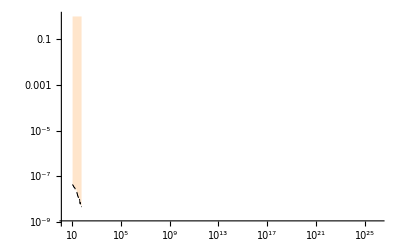

```mathematica
CMS201830part3= Import["/Users/alfre/Documents/GitHub/DarkPhoton_Limits/Limit_epsvsmass_BrHtoGamD_30_2018data_m0to60_observed_part3.dat","Table"]
CMS201830part3plot = ListLogLogPlot[DataConvertertest[CMS201830part3],Joined->True,PlotStyle->{(*Lighter[Orange,0.3]*)Black,Thickness[0.0015],Dashed},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Lighter[Orange,0.6]],PlotRange->{10^-9,1}]
```

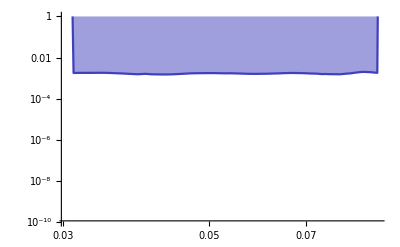

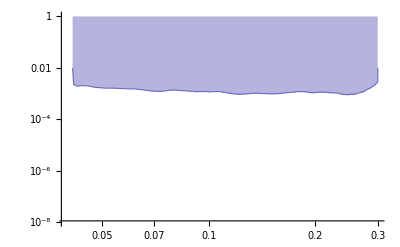

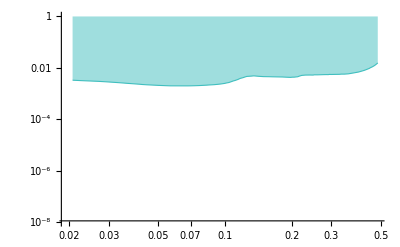

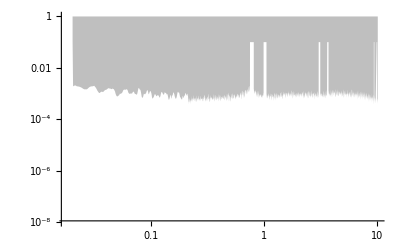

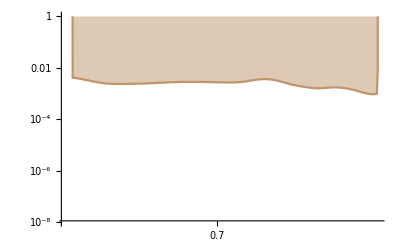

```mathematica
SetDirectory[NotebookDirectory[]];


mμ=0.1057 GeV;
me=0.000511*GeV;
α=1/137.0;
inCM={GeV->5.0677 10^13/CM};
inSec={GeV->1.51926778 10^24/seconds};
SaveRdataMod=Import["data/SaveRdataMod.txt","Table"];

Rhad[m_]:=If[m<.36,0,Interpolation[SaveRdataMod,InterpolationOrder->1][m]]

electronWidthFunction[mA_]:=√(1-4 me^2/(mA^2*GeV^2));
muonWidthFunction[mA_]:=√Max[1-4 mμ^2/(mA^2*GeV^2),0]
totalWidthFunction[mA_]:=√(1-4 me^2/(mA^2*GeV^2))+√Max[1-4 mμ^2/(mA^2*GeV^2),0]  (1+Rhad[mA])
muonfraction[mA_]:=muonWidthFunction[mA]/totalWidthFunction[mA]
SigmaAOnShell[Ecm_,alpha_,alphaD_,epsilon_,mL_,mA_,thetamin_]:=0.3894*10^(-3+15)*4*π*epsilon^2*alpha^2*1/Ecm^2*(1-mA^2/Ecm^2)*((2+(4*mA^2)/(Ecm^2*(1-mA^2/Ecm^2)^2))*Log[2/thetamin]-1+1/8*(2-(4*mA^2)/(Ecm^2*(1-mA^2/Ecm^2)^2))*thetamin^2)
Fmts[label_,color_,{x_,y_},size_,colorbackground_]:=Inset[Style[label,FontSize->size,color],Scaled[{x,y}],Background->colorbackground]
Lifetime[ϵ_,mA_]:=3/(α ϵ^2 mA) 1/totalWidthFunction[mA/GeV];
inCM={GeV->5.0677 10^13/CM};

Clear[DataConverterWithCommaDropper]
DataConverterWithCommaDropper[data_]:=Table[{10^ToExpression[StringDrop[data[[i]][[1]],-1]],10^data[[i,2]]},{i,1,Length[data]}]
(* To convert Subscript[Log, 10] Mass to Mass and Subscript[Log, 10] ϵ  to ϵ: *)
DataConverter[data_]:=Table[{10^data[[i,1]],10^data[[i,2]]},{i,1,Length[data]}]
(* To convert Subscript[Log, 10] Mass to Mass and Subscript[Log, 10] ϵ  to ϵ, and to convert 90% c.l. limit to 95% c.l. limit on epsilon: *)
DataConvertercl90to95[data_]:=Table[{10^data[[i,1]],(2/1.64)^(1/4)10^data[[i,2]]},{i,1,Length[data]}]
(* To convert MeV to GeV and epsilon^2 to epsilon: *)
DataConverter2[data_]:=Table[{data[[i,1]]/1000,√data[[i,2]]},{i,1,Length[data]}]
(* To convert MeV to GeV: *)
DataConverter3[data_]:=Table[{data[[i,1]]/1000,data[[i,2]]},{i,1,Length[data]}]
(* To convert MeV to GeV and epsilon^2 to epsilon, and to convert 90% c.l. limit to 95% c.l. limit on epsilon: *)
DataConverter2cl90to95[data_]:=Table[{data[[i,1]]/1000,(2/1.64)^(1/4)√data[[i,2]]},{i,1,Length[data]}]


myopacity=0.5;
myopacityae=0.3;

mycolor=Blend[{Lighter[Blue],Gray}];
mycolor2=Blend[{Blue,Gray}];

mycolorsn=Blend[{Lighter[Blue],Gray}];
mycolor2sn=Blend[{Blue,Gray}];

mycolore137=Lighter[Gray];(*Blend[{Lighter[Orange],Gray}];*)
mycolor2e137=Lighter[Gray];(*Blend[{Orange,Gray}];*)

mycolore141=Lighter[Gray];(*Blend[{Lighter[Orange],Gray}];*)
mycolor2e141=Lighter[Gray];(*Blend[{Orange,Gray}];*)

mycolore774=Lighter[Gray];(*Blend[{Lighter[Orange],Gray}];*)
mycolor2e774=Lighter[Gray];(*Blend[{Orange,Gray}];*)

mycolororsay=Lighter[Gray];(*Blend[{Lighter[Orange],Gray}];*)
mycolor2orsay=Lighter[Gray];(*Blend[{Orange,Gray}];*)

mycolorA12011=Blend[{Lighter[Purple],Gray}];
mycolor2A12011=Blend[{Purple,Gray}];

mycolorapex2011=Blend[{Lighter[Purple],Gray}];
mycolor2apex2011=Blend[{Purple,Gray}];

mycolorU70=Lighter[Gray];(*Blend[{Lighter[Orange],Gray}];*)
mycolor2U70=Lighter[Gray];(*Blend[{Orange,Gray}];*)

mycolorcharm=Lighter[Gray];(*Blend[{Lighter[Orange],Gray}];*)
mycolor2charm=Lighter[Gray];(*Blend[{Orange,Gray}];*)

mycolorKLOE2012conservative=Blend[{Lighter[Orange],Gray}];
mycolor2KLOE2012conservative=Blend[{Orange,Gray}];

mycolorKLOE2012optimistic=Blend[{Lighter[Orange],Gray}];
mycolor2KLOE2012optimistic=Blend[{Orange,Gray}];

mycolorLHCb2018 = Blend[{Lighter[Blue],Lighter[Purple]}];

(*mycolorBabar1=Blend[{Lighter[Orange],Gray}];
mycolor2Babar1=Blend[{Orange,Gray}];*)

mycolorBabar1=Gray;
mycolor2Babar1=Gray;

mycoloraμlimit5σ=Blend[{Lighter[Cyan],Gray}];
mycolor2aμlimit5σ=Blend[{Cyan,Gray}];

mycoloraμ2σBand=Blend[{Green,Gray}];
mycolor2aμ2σBand=Blend[{Darker[Green],Gray}];

mycolorae95clLimit=Blend[{Lighter[Red],Gray}];
mycolor2ae95clLimit=Blend[{Red,Gray}];

mycolorlsnd=Lighter[Lighter[Gray]];(*Blend[{Lighter[Orange],Gray}];*)
mycolor2lsnd=Lighter[Lighter[Gray]];(*Blend[{Orange,Gray}];*)

mycolorwasacosy2010=Blend[{Lighter[Orange],Gray}];
mycolor2wasacosy2010=Blend[{Orange,Gray}];

mycolormodelindependent=Blend[{Lighter[Orange],Gray}];
mycolor2modelindependent=Blend[{Orange,Gray}];


sn=Import["data/SN.txt","Table"];
sn1=Take[sn,{1,38}];
sn2=Take[sn,{39,Length[sn]}];
snplot=ListLogLogPlot[{sn1,sn2},Joined->True,PlotStyle->{mycolorsn,mycolorsn},Filling->{1->{2}},FillingStyle->Directive[Opacity[myopacity],mycolor]];
snplotL=ListLogLogPlot[{sn1,sn2},Joined->True,PlotStyle->{mycolor2sn,mycolor2sn}];



e137=Import["data/E137_Andreas.dat","Table"];
e1371=Take[DataConverterWithCommaDropper[e137],{1,352}];
e1372=Sort[Take[DataConverterWithCommaDropper[e137],{353,Length[e137]}]];
e137plot=ListLogLogPlot[{e1371,e1372},Joined->True,PlotStyle->{mycolore137,mycolore137},Filling->{1->{2}},FillingStyle->Directive[Opacity[myopacity],mycolore137]];
e137plotL=ListLogLogPlot[{e1371,e1372},Joined->True,PlotStyle->{mycolor2e137,mycolor2e137}];



e141=Import["data/E141_Andreas.dat","Table"];
e1411=Take[DataConverterWithCommaDropper[e141],{1,186}];
e1412=Sort[Take[DataConverterWithCommaDropper[e141],{187,Length[e141]}]];
e141plot=ListLogLogPlot[{e1411,e1412},Joined->True,PlotStyle->{mycolore141,mycolore141},Filling->{1->{2}},FillingStyle->Directive[Opacity[myopacity],mycolore141]];
e141plotL=ListLogLogPlot[{e1411,e1412},Joined->True,PlotStyle->{mycolor2e141,mycolor2e141}];



e774=Import["data/E774_Andreas.dat","Table"];
e7741=Take[DataConverterWithCommaDropper[e774],{1,144}];
e7742=Sort[Take[DataConverterWithCommaDropper[e774],{145,Length[e774]}]];
e774plot=ListLogLogPlot[{e7741,e7742},Joined->True,PlotStyle->{mycolore774,mycolore774},Filling->{1->{2}},FillingStyle->Directive[Opacity[myopacity],mycolore774]];
e774plotL=ListLogLogPlot[{e7741,e7742},Joined->True,PlotStyle->{mycolor2e774,mycolor2e774}];



orsay=Import["data/Orsay_Andreas.dat","Table"];
orsay1=Take[DataConverterWithCommaDropper[orsay],{1,276}];
orsay2=Sort[Take[DataConverterWithCommaDropper[orsay],{277,Length[orsay]}]];
orsayplot=ListLogLogPlot[{orsay1,orsay2},Joined->True,PlotStyle->{mycolororsay,mycolororsay},Filling->{1->{2}},FillingStyle->Directive[Opacity[myopacity],mycolororsay]];
orsayplotL=ListLogLogPlot[{orsay1,orsay2},Joined->True,PlotStyle->{mycolor2orsay,mycolor2orsay}];




(* Convert MAMI limit from 90% c.l. to 95% c.l. on epsilon by multiplying by (2/1.64)^(1/4), i.e. using DataConvertercl90to95 *)
A12011=DataConvertercl90to95[Import["data/A1_2011.dat","Table"]];
A12011plot=ListLogLogPlot[A12011,Joined->True,PlotStyle->mycolorA12011,Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],mycolorA12011]];
A12011plotL=ListLogLogPlot[A12011,Joined->True,PlotStyle->mycolor2A12011];




U70=Join[Import["data/U70-Serpukhov.txt","Table"],{{0.13889,4.9088072777*^-7}}];(* added a point at the end to close curve properly *)
U701=Take[U70,{1,33}];
U702=Take[U70,{34,Length[U70]}];
U70plot=ListLogLogPlot[{U701,U702},Joined->True,PlotStyle->{mycolorU70,mycolorU70},Filling->{1->{2}},FillingStyle->Directive[Opacity[myopacity],mycolorU70]];
U70plotL=ListLogLogPlot[{U701,U702},Joined->True,PlotStyle->{mycolor2U70,mycolor2U70}];




KLOE2012conservative=DataConverter2[Import["data/KLOE-conservative.txt","Table"]];
KLOE2012conservativeplot=ListLogLogPlot[KLOE2012conservative,Joined->True,PlotStyle->mycolorKLOE2012conservative,Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],mycolorKLOE2012conservative]];
KLOE2012conservativeplotL=ListLogLogPlot[KLOE2012conservative,Joined->True,PlotStyle->mycolor2KLOE2012conservative];




KLOE2012optimistic=DataConverter2[Import["data/KLOE-optimistic.txt","Table"]];
KLOE2012optimisticplot=ListLogLogPlot[KLOE2012optimistic,Joined->True,PlotStyle->mycolorKLOE2012optimistic,Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],mycolorKLOE2012optimistic]];
KLOE2012optimisticplotL=ListLogLogPlot[KLOE2012optimistic,Joined->True,PlotStyle->mycolor2KLOE2012optimistic];



(* LHCb limit 2017 paper https://journals.aps.org/prl/abstract/10.1103/PhysRevLett.120.061801*)

LHCb2018 = DataConverter2[Import["data/prompt-excluded_LHCb2018.txt","Table"]];
LHCb2018plot = ListLogLogPlot[LHCb2018,Joined->True,PlotStyle->mycolorLHCb2018,Filling->{1->Top},
FillingStyle->Directive[Opacity[myopacity],mycolorLHCb2018]];


(* LHCb limit 2017 paper https://journals.aps.org/prl/abstract/10.1103/PhysRevLett.120.061801*)

LHCb2018longlived1 = DataConverter2[Import["data/long-lived-excluded_LHCb2018_region1.txt","Table"]];
LHCb2018longlived1plot = ListLogLogPlot[LHCb2018longlived1,Joined->True,PlotStyle->mycolorLHCb2018,Filling->{1->Top},
FillingStyle->Directive[Opacity[myopacity],mycolorLHCb2018]];

LHCb2018longlived2 = DataConverter2[Import["data/long-lived-excluded_LHCb2018_region2.txt","Table"]];
LHCb2018longlived2plot = ListLogLogPlot[LHCb2018longlived2,Joined->True,PlotStyle->mycolorLHCb2018,Filling->{1->Top},
FillingStyle->Directive[Opacity[myopacity],mycolorLHCb2018]];

LHCb2018longlived3 = DataConverter2[Import["data/long-lived-excluded_LHCb2018_region3.txt","Table"]];
LHCb2018longlived3plot = ListLogLogPlot[LHCb2018longlived3,Joined->True,PlotStyle->mycolorLHCb2018,Filling->{1->Top},
FillingStyle->Directive[Opacity[myopacity],mycolorLHCb2018]];

LHCb2018longlived4 = DataConverter2[Import["data/long-lived-excluded_LHCb2018_region4.txt","Table"]];
LHCb2018longlived4plot = ListLogLogPlot[LHCb2018longlived4,Joined->True,PlotStyle->mycolorLHCb2018,Filling->{1->Top},
FillingStyle->Directive[Opacity[myopacity],mycolorLHCb2018]];


(* 90% BR limit from 0902.2176: *)
(* Do 200 MeV -- 1 GeV data approximately accurately, but then add a few data points at the end that roughly interpolates among the BaBar results *)
BabarBR=Join[Import["data/Babar-1.txt","Table"],{{1.,10.^-6},{4.,10.^-6},{9.3,3. 10^-6}}];
(* No of events that BaBar is sensitive to equals (121.8±1.2)×10^6 Upsilon(3S) decays times Branching Ratio Constraint in 0902.2176 *)
(* Convert from 90% c.l. limit to 95% c.l. limit on epsilon by multiplying by (2/1.64)^(1/4) *)
Babar1=Table[{BabarBR[[i,1]],(2/1.64)^(1/4)√((BabarBR[[i,2]]*121.8 10^6)/(30*SigmaAOnShell[10.58,1/137.0,1,1.0(*epsilon*),1.0,BabarBR[[i,1]],ArcCos[0.9]]*muonfraction[BabarBR[[i,1]]]))},{i,1,Length[BabarBR]}];
Babar1plot=ListLogLogPlot[Babar1,Joined->True,PlotRange->{10^-4,10^-1},PlotStyle->mycolorBabar1,Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],mycolorBabar1]];
Babar1plotL=ListLogLogPlot[Babar1,Joined->True,PlotStyle->mycolor2Babar1];




(* Convert APEX limit from 90% c.l. to 95% c.l. on epsilon by multiplying by (2/1.64)^(1/4), i.e. using DataConverter2cl90to95 *)
apex2011=Join[{{0.177024,0.01}},DataConverter2cl90to95[Import["data/epsilon_PCL_6_30_10_27.txt","Table"]],{{0.249776,0.01}}]; (* added point at beginning and end to make curve go up to 10^-2 *)
apex2011plot=ListLogLogPlot[apex2011,Joined->True,PlotStyle->mycolorapex2011,Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],mycolorapex2011]];
apex2011plotL=ListLogLogPlot[apex2011,Joined->True,PlotStyle->mycolor2apex2011];




(* anomalous magnetic moment of muon: g-2 (constraint taken from Pospelov (arXiv:0811.1030[hep-ph]))*)
gminus2[alpha_,ϵ_,mA_,ml_]:=alpha/(2*π)*ϵ^2*NIntegrate[(2*ml^2*z*(1-z)^2)/(ml^2*(1-z)^2+mA^2*z),{z,0,1}]
(*use results from: 1010.4180, Eq. 22 and following paragraph; based on e+e- data, gives 3.6-sigma;  numbers here are in units of 10^-10
Subscript[a, SM] = 11659180.2 ± 4.2 ± 2.6 ± 0.2 (4.9)
Subscript[a, exp] = 11 659 208.9 ± 5.4 ± 3.3
Difference is 28.7 ± 8.0 (3.6 σ)*)

aμlimit5σ=Table[{masses,√(((28.7+5*8.0)*10^-10)/gminus2[1/137,1.,masses,mμ/GeV])},{masses,0.001,5.0,0.01}];
aμ2σHigh=Table[{masses,√(((28.7+2*8.0)*10^-10)/gminus2[1/137,1.,masses,mμ/GeV])},{masses,0.001,8.0,0.01}];
aμ2σLow=Table[{masses,√(((28.7-2*8.0)*10^-10)/gminus2[1/137,1.,masses,mμ/GeV])},{masses,0.001,8.0,0.01}];



aμlimit5σplot=ListLogLogPlot[aμlimit5σ,Joined->True,PlotStyle->mycoloraμlimit5σ,Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],mycoloraμlimit5σ]];
aμlimit5σplotL=ListLogLogPlot[aμlimit5σ,Joined->True,PlotStyle->mycolor2aμlimit5σ];
aμ2σBandplot=ListLogLogPlot[{aμ2σLow,aμ2σHigh},Joined->True,PlotStyle->mycoloraμ2σBand,Filling->{1->{2}},FillingStyle->Directive[Opacity[myopacity],mycoloraμ2σBand]];
aμ2σBandplotL=ListLogLogPlot[{aμ2σLow,aμ2σHigh},Joined->True,PlotStyle->mycoloraμ2σBand];




(*Electron anomaous magnetic moment:
Discrepancy between Experimental Measurement and Standard Model is: 
Subscript[Δa, e] = Subscript[a, exp]-Subscript[a, SM] = -1.06 (0.82) × 10^-12*)
ae90clLimit=Table[{masses,√(((-1.06+1.64*0.82)*10^-12)/gminus2[1/137,1.,masses,me/GeV])},{masses,0.001,1.0,0.01}];
ae90cllimitplot=ListLogLogPlot[ae90clLimit,Joined->True,PlotStyle->mycolor,Filling->{1->Top},FillingStyle->mycolor,PlotRange->{{0.001,1},{10^-6,10^-1}},Frame->True];
ae90cllimitplotL=ListLogLogPlot[ae90clLimit,Joined->True,PlotStyle->{mycolor2ae95clLimit,Dashed},PlotRange->{{0.001,1},{10^-6,10^-1}},Frame->True];
ae95clLimit=Table[{masses,√(((-1.06+2*0.82)*10^-12)/gminus2[1/137,1.,masses,me/GeV])},{masses,0.001,5.0,0.01}];
ae95cllimitplot=ListLogLogPlot[ae95clLimit,Joined->True,PlotStyle->mycolorae95clLimit,Filling->{1->Top},FillingStyle->Directive[Opacity[myopacityae],mycolorae95clLimit],PlotRange->{{0.001,1},{10^-6,10^-1}},Frame->True];
ae95cllimitplotL=ListLogLogPlot[ae95clLimit,Joined->True,PlotStyle->mycolor2ae95clLimit,PlotRange->{{0.001,1},{10^-6,10^-1}},Frame->True];
ae3σLimit=Table[{masses,√(((-1.06+3*0.82)*10^-12)/gminus2[1/137,1.,masses,me/GeV])},{masses,0.001,1.0,0.01}];
ae3σlimitplot=ListLogLogPlot[ae3σLimit,Joined->True,PlotStyle->mycolor,Filling->{1->Top},FillingStyle->mycolor,PlotRange->{{0.001,1},{10^-6,10^-1}},Frame->True];
ae3σlimitplotL=ListLogLogPlot[ae3σLimit,Joined->True,PlotStyle->{mycolor2ae95clLimit,DotDashed},PlotRange->{{0.001,1},{10^-6,10^-1}},Frame->True];
ae5σLimit=Table[{masses,√(((-1.06+5*0.82)*10^-12)/gminus2[1/137,1.,masses,me/GeV])},{masses,0.001,1.0,0.01}];
ae5σlimitplot=ListLogLogPlot[ae5σLimit,Joined->True,PlotStyle->mycolor,Filling->{1->Top},FillingStyle->mycolor,PlotRange->{{0.001,1},{10^-6,10^-1}},Frame->True];
ae5σlimitplotL=ListLogLogPlot[ae5σLimit,Joined->True,PlotStyle->{mycolor2ae95clLimit,Dotted},PlotRange->{{0.001,1},{10^-6,10^-1}},Frame->True];

mycolorae3σLimit2014=Blend[{Lighter[Red],Gray}];
ae3σLimit2014=Import["data2014/ae3σLimit.txt","Table"];
ae3σlimitplot2014=ListLogLogPlot[ae3σLimit2014,Joined->True,PlotStyle->mycolorae3σLimit2014,Filling->{1->Top},FillingStyle->Directive[Opacity[myopacityae],mycolorae3σLimit2014],PlotRange->{{0.001,1},{10^-6,1}},Frame->True];



lsnd=Import["data/lsnd.txt","Table"];
lsnd1=Join[Take[lsnd,{1,41}],{{0.2004062831,2.9850926399*^-7}}]; (* add a point to make curve smooth *)
lsnd2=Sort[Take[lsnd,{42,Length[lsnd]}]];
lsndplot=ListLogLogPlot[{lsnd1,lsnd2},Joined->True,PlotStyle->{mycolorlsnd,mycolorlsnd},Filling->{1->{2}},FillingStyle->Directive[Opacity[myopacity],mycolorlsnd]];
lsndplotL=ListLogLogPlot[{lsnd1,lsnd2},Joined->True,PlotStyle->{mycolor2lsnd,mycolor2lsnd}];




wasacosy2010=Join[{{0.0013065973520000002,0.1}},DataConverter2[Import["data/wasa-cosy.txt","Table"]],{{0.0983349304199,0.1}}] ;(* added first and last point to make curve go to axis nicely*)
wasacosy2010plot=ListLogLogPlot[wasacosy2010,Joined->True,PlotStyle->mycolorwasacosy2010,Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],mycolorwasacosy2010]];
wasacosy2010plotL=ListLogLogPlot[wasacosy2010,Joined->True,PlotStyle->mycolor2wasacosy2010];




modelindependent=Import["data/model-independent.txt","Table"];
modelindependentplot=ListLogLogPlot[modelindependent,Joined->True,PlotStyle->mycolormodelindependent,Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],mycolormodelindependent]];
modelindependentplotL=ListLogLogPlot[modelindependent,Joined->True,PlotStyle->mycolor2modelindependent];



charm=DataConverter3[Import["data/charm.txt","Table"]];
charm1=Join[{{0.001,10^-5.95}},Take[charm,{1,33}]];(*added point somewhat arbitrarily to extend plot to 1 MeV*)
charm2=Join[{{0.001,0.0004}},Take[charm,{34,Length[charm]}]];(*added point somewhat arbitrarily to extend plot to 1 MeV*)

(* CONVERT THE LOWER LINE FROM A 90% C.L. UPPER LIMIT (BASED ON 2.3 EVENTS OBSERVED IN 1204.3583) TO A 95% C.L. UPPER LIMIT BASED ON A FELDMAN COUSINS NUMBER OF 3.09 EVENTS; CAN ONLY DO THIS FOR LOWER LINE, SINCE UPPER LINE IS LIMITED BY LIFETIME NOT BY STATISTICS *)
charm1=Table[{charm1[[i,1]],√(3.09/2.3)charm1[[i,2]]},{i,1,Length[charm1]}];
charmplot=ListLogLogPlot[{charm1,charm2},Joined->True,PlotStyle->{mycolorcharm,mycolorcharm},Filling->{1->{2}},FillingStyle->Directive[Opacity[myopacity],mycolorcharm]];
charmplotL=ListLogLogPlot[{charm1,charm2},Joined->True,PlotStyle->{mycolor2charm,mycolor2charm}];





myPhenix=Blend[{Blue,Gray}];
phenix2014=Join[{{0.031,1}},DataConverter2cl90to95[Import["data2014/Phenix2014.txt","Table"]],{{0.09,1}}];(* added point at beginning and end to make curve go up to 10^-1 *)
phenix2014plot=ListLogLogPlot[phenix2014,Joined->True,PlotStyle->myPhenix,Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],myPhenix],PlotRange->{10^-10,1}];

phenix2014plot


Mainz2014Data=Import["data2014/Mainz-2014.txt","Table"];
Mainz2014Data2=Table[{Mainz2014Data[[i,1]],√Mainz2014Data[[i,2]]},{i,1,Length[Mainz2014Data]}];
Mainz2014Plot=ListLogLogPlot[Mainz2014Data2,Joined->True,PlotStyle->{Blend[{Gray,Lighter[Blue]}],Thickness[0.002]},Filling->{1->Top},PlotRange->{10^-8,1},FillingStyle->Directive[Opacity[myopacity],Blend[{Gray,Lighter[Blue]}]]];

Mainz2014Plot

Hades2013Data=Import["data2014/Hades.txt","Table"];
Hades2013Data2=Table[{Hades2013Data[[i,1]],(1.96/1.64)^(1/2)√Hades2013Data[[i,2]]},{i,1,Length[Hades2013Data]}];
Hades2013Plot=ListLogLogPlot[Hades2013Data2,Joined->True,PlotStyle->{Blend[{Cyan,Gray}],Thickness[0.002]},Filling->{1->Top},PlotRange->{10^-8,1},FillingStyle->Directive[Opacity[myopacity],Blend[{Cyan,Gray}]]];

Hades2013Plot


babar2014Data=Import["data2014/BabarNew95.txt","Table"];
babar2014PlotL=ListLogLogPlot[babar2014Data,Joined->True,PlotStyle->{Thickness[0.005],(*Blend[{Orange,Gray}]*)Gray},PlotRange->{10^-10,1}];
babar2014Plot=ListLogLogPlot[babar2014Data,Joined->True,PlotStyle->{(*Blend[{Orange,Gray}]*)Gray,Thickness[0.0001]},Filling->{1->Top},PlotRange->{10^-8,1},FillingStyle->Directive[Opacity[myopacity],(*Blend[{Orange,Gray}]*)Gray]];
babar2014Plot2=ListLogLogPlot[babar2014Data,Joined->True,PlotStyle->None,Filling->{1->Top},PlotRange->{10^-8,1},FillingStyle->Directive[Opacity[myopacity],(*Blend[{Orange,Gray}]*)Gray]];
babar2014PlotNoLines=ListLogLogPlot[babar2014Data,Joined->True,PlotStyle->None,Filling->{1->Top},PlotRange->{10^-8,1},FillingStyle->Directive[Opacity[myopacity],(*Blend[{Orange,Gray}]*)Gray]];

babar2014PlotNoLines



KLOE2014=Import["data2014/KLOE-2014.txt","Table"];
KLOE20142=DataConverter2cl90to95[Join[{{517.9,1}},KLOE2014,{{979.9,1}}]]; (*added point at beginning and end to make it go to 1*)
KLOE2014plot=ListLogLogPlot[KLOE20142,Joined->True,PlotStyle->{mycolorKLOE2012optimistic},Filling->{1->Top},PlotRange->{10^-8,1},FillingStyle->Directive[Opacity[myopacity],Blend[{Lighter[Orange],Gray}]]];

KLOE2014plot
```

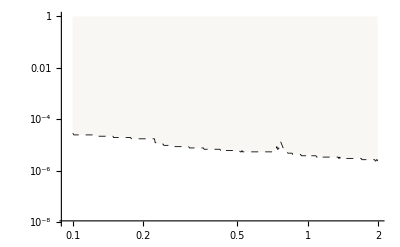

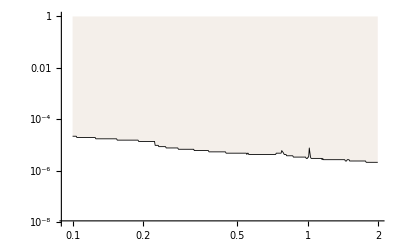

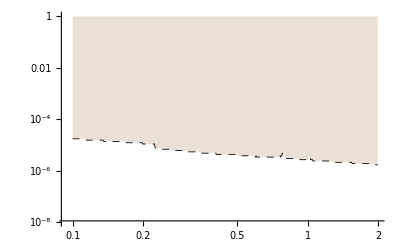

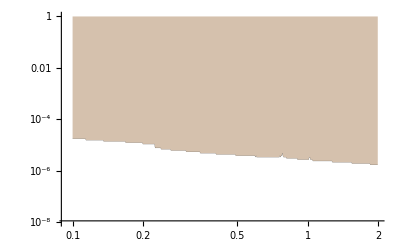

```mathematica
ATLAS05prompt = Import["data/ATLAS05.txt","Table"];
ATLAS05promptplot =  ListLogLogPlot[ATLAS05prompt,Joined->True,PlotStyle->{(*Lighter[Brown,0.9]*)Black,Thickness[0.0015],Dashed},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Lighter[Brown,0.9]],PlotRange->{10^-8,1}]
ATLAS10prompt = Import["data/ATLAS10.txt","Table"];
ATLAS10promptplot =  ListLogLogPlot[ATLAS10prompt,Joined->True,PlotStyle->{(*Lighter[Brown,0.8]*)Black,Thickness[0.0015]},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Lighter[Brown,0.8]],PlotRange->{10^-8,1}]
ATLAS20prompt = Import["data/ATLAS20.txt","Table"];
ATLAS20promptplot =  ListLogLogPlot[ATLAS20prompt,Joined->True,PlotStyle->{(*Lighter[Brown,0.6]*)Black,Thickness[0.0015],Dashed},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Lighter[Brown,0.6]],PlotRange->{10^-8,1}]
ATLAS40prompt = Import["data/ATLAS40.txt","Table"];
ATLAS40promptplot =  ListLogLogPlot[ATLAS20prompt,Joined->True,PlotStyle->{(*Lighter[Brown,0.2]*)Black,Thickness[0.0001]},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Lighter[Brown,0.2]],PlotRange->{10^-8,1}]
```

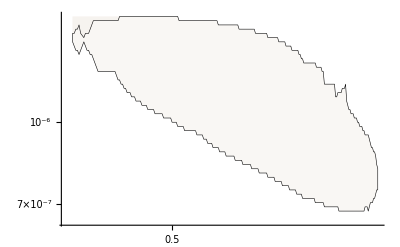

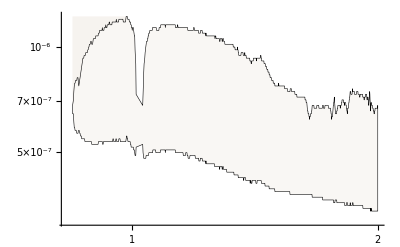

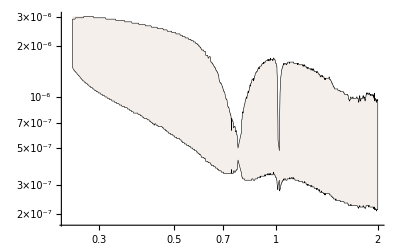

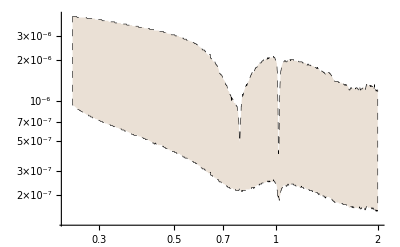

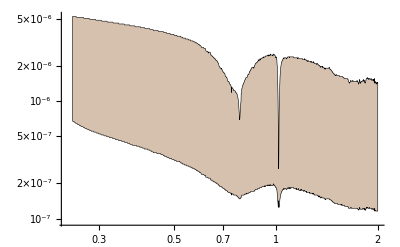

```mathematica
ATLAS20145a = Import["data2014/g_ATLAS5a.txt","Table"];
ATLAS20145aplot = ListLogLogPlot[ATLAS20145a,Joined->True,PlotStyle->{(*Lighter[Brown,0.9]*)Black,Thickness[0.0010]},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Lighter[Brown,0.9]]]
ATLAS20145b = Import["data2014/g_ATLAS5b.txt","Table"];
ATLAS20145bplot = ListLogLogPlot[ATLAS20145b,Joined->True,PlotStyle->{(*Lighter[Brown,0.9]*)Black,Thickness[0.0010]},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Lighter[Brown,0.9]]]
ATLAS201410 = Import["data2014/g_ATLAS10.txt","Table"];
ATLAS201410plot = ListLogLogPlot[ATLAS201410,Joined->True,PlotStyle->{(*Lighter[Brown,0.8]*)Black,Thickness[0.0010]},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Lighter[Brown,0.8]]]
ATLAS201420 = Import["data2014/g_ATLAS20.txt","Table"];
ATLAS201420plot = ListLogLogPlot[ATLAS201420,Joined->True,PlotStyle->{(*Lighter[Brown,0.6]*)Black,Thickness[0.0010],Dashed},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Lighter[Brown,0.6]]]
ATLAS201440 = Import["data2014/g_ATLAS40.txt","Table"];
ATLAS201440plot = ListLogLogPlot[ATLAS201440,Joined->True,PlotStyle->{(*Lighter[Brown,0.2]*)Black,Thickness[0.0010]},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Lighter[Brown,0.2]]]
```

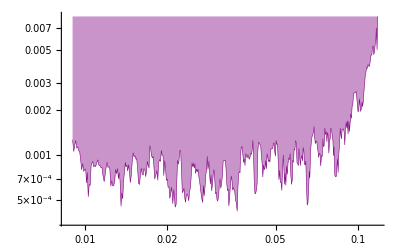

```mathematica
NA48 = Import["data/NA48.txt","Table"];
NA48plot = ListLogLogPlot[NA48,Joined->True,PlotStyle->{(*Lighter[Brown,0.2]*)Purple,Thickness[0.0010]},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Blend[{Lighter[Purple],Purple}]]]
```

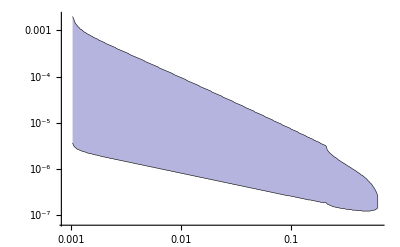

General::stop: Further output of ListLogLogPlot::lpn will be suppressed during this calculation.

ListLogLogPlot::lpn: Null is not a list of numbers or pairs of numbers.

Import::nffil: File not found during Import.

Blend::arg: RGBColor[0, 1, 1] is not a valid list of colors or images, or pairs of a real number and a color or an image.

Import::nffil: File not found during Import. ButtonBox["»",
Appearance->{Automatic, None},
BaseStyle->"Link",
ButtonData:>"paclet:ref/message/Import/nffil",
ButtonNote->"Import::nffil"]

```mathematica
nucal = Import["data/nucaltemp2.txt","Table"];
nucalplot = ListLogLogPlot[nucal,Joined->True,PlotStyle->{(*Lighter[Brown,0.2]*)Black,Thickness[0.0010],solid},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Blend[{Lighter[Blue],Gray}]]]
```

```mathematica
Clear[fticksR,fticksR2,fticksR3,PrettyExp,PrettyExpR2]
PrettyExp[x_,MAX_:2]:=If[Abs[x]≥MAX,Superscript[10,x],If[x≥0,10^x,10.^x]]
(* Axis for Epsilon versus mass: *)
fticksR[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{i*10.^x,"",{.008,0}},{i,2,9}],{1}],{10.^x,PrettyExp[x,AMAX],{.02,0}}],{x,Floor[Log[10,min]],Ceiling[Log[10,max]],1}],1]
PrettyExpR2[x_,MAX_:2]:=If[Abs[x]>MAX,Superscript[10,2x],If[x≥0,10^x,10.^x]]
(* Axis for Epsilon^2 versus mass *)fticksR2[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{10.^(x+Log[10,i]/2)," ",{.008,0}},{i,2,10}],{1}],{10.^x,PrettyExpR2[x,AMAX],{.02,0}}],{x,Ceiling[Log[10,min]],Floor[Log[10,max]],1/2}],1]
(* Axis for Epsilon^2 versus mass, but with y-axis labels only every 2 decades *)
fticksR3[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{If[i≤10,10.^(x+Log[10,i]/2),10.^(0.5+x+Log[10,i-10]/2)]," ",{If[i==10,0.02,0.008],0}},{i,2,20}],{1}],{10.^x,PrettyExpR2[x,AMAX],{.02,0}}],{x,Ceiling[Log[10,min]],Floor[Log[10,max]],1}],1]
```

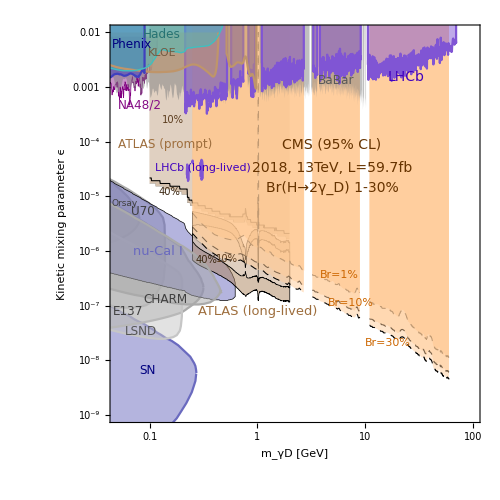

Export::nodir: Directory C:\Users\alfre\Documents\GitHub\DarkPhoton_Limits\plots\ does not exist.

Export::noopen: Cannot open plots/AllConstraints-11-14-12.pdf.

```mathematica
mylegendplot9GeV=LogLogPlot[1,{m,0.001,100},Frame->True,PlotRange->{{0.05,100},{10^-9,0.99 10^-2}},FrameTicks->{Automatic,(*fticks2[10^-11,10^-1,1]*)(*fticksR[10^-11,10^-2,0]*)Automatic},FrameLabel->{Row[{Spacer@315,"m_γD [GeV]"}],Row[{Spacer@150,"Kinetic mixing parameter ϵ"}]},LabelStyle->22,
Epilog->{
(*Inset[Style["Orsay",FontSize->12,Black],Scaled[{0.3,0.59}]],*)
(* 95% c.l. *) Inset[Style["U70",FontSize->12,Blend[{Gray,Black}]],Scaled[{0.089,0.53}]],
(* 95% c.l. *) Inset[Style["Orsay",FontSize->9,Blend[{Gray,Black}]],Scaled[{0.040,0.55}]],
(* 95% c.l. *) Inset[Style["E137",FontSize->12,Blend[{Gray,Black}]],Scaled[{0.05,0.28}]],
(* 95% c.l. *) (*Inset[Style["E141",FontSize->12,Blend[{Gray,Black}]],Scaled[{0.05,0.8}]],*)
(* 95% c.l. *)(*Inset[Style["E774",FontSize->12,Blend[{Gray,Black}]],Scaled[{0.07,0.87}]],*)
(* 95% c.l. *) Inset[Style["CHARM",FontSize->12,Blend[{Gray,Black}]],Scaled[{0.15,0.31}]],
(* 95% c.l. *) Inset[Style["nu-Cal I",FontSize->13, Blend[{Lighter[Blue],Gray}]],Scaled[{0.13,0.43}]],
(* 5σ c.l. *) (*Inset[Style["a_(μ,  5 σ)",FontSize->12,Blend[{Cyan,Black}]],Scaled[{0.2,0.96}]],*)
(* 95% c.l. band *)(*Inset[Rotate[Style["a_(μ, ±2σ) favored",FontSize->12,Blend[{Green,Black}]],5°],Scaled[{0.11,0.89}]],*)
(* 95% c.l. *)Inset[Style["Phenix",FontSize->12,Blend[{Blue,Black}]],Scaled[{0.06,0.95}]],
(* 95% c.l. *)Inset[Style["Hades",FontSize->12,Darker[Blend[{Cyan,Gray}],0.4]],Scaled[{0.14,0.975}]],
(* 95% c.l. *)(*Inset[Style["a_e",FontSize->12,Blend[{Red,Black}]],Scaled[{0.1,0.86}]],*)
(* 95% c.l. *) Inset[Style["BaBar",FontSize->12, Darker[Gray,0.3]],Scaled[{0.61,0.86}]],
(* 95% c.l. *) Inset[Style["CMS (95% CL)",FontSize->14,Darker[Orange,0.6]],Scaled[{0.60,0.70}]],
(* 95% c.l. *) Inset[Style["2018, 13TeV, L=59.7fb",FontSize->14,Darker[Orange,0.6]],Scaled[{0.60,0.64}]],
(* 95% c.l. *) Inset[Style["Br(H→2γ_D) 1-30%",FontSize->14,Darker[Orange,0.6]],Scaled[{0.60,0.59}]],
(* 95% c.l. *) Inset[Style["LHCb",FontSize->14,Blend[{Blue,Purple}]],Scaled[{0.80,0.87}]],
(* 95% c.l. *) Inset[Style["LHCb (long-lived)",FontSize->11,Blend[{Blue,Purple}]],Scaled[{0.25,0.64}]],
(*Inset[Style["0.1%",FontSize->12,(*Blend[{Purple,Black}]*)Darker[Orange,0.5]],Scaled[{0.22,0.70}]],*)
Inset[Style["Br=1%",FontSize->11,(*Blend[{Purple,Black}]*)Darker[Orange,0.2]],Scaled[{0.62,0.37}]],
Inset[Style["Br=10%",FontSize->11,(*Blend[{Purple,Black}]*)Darker[Orange,0.2]],Scaled[{0.65,0.30}]],
Inset[Style["Br=30%",FontSize->11,(*Blend[{Purple,Black}]*)Darker[Orange,0.2]],Scaled[{0.75,0.20}]],
(* 95% c.l. *) Inset[Style["ATLAS (long-lived)",FontSize->13,Lighter[Brown,0.05]],Scaled[{0.40,0.28}]],
(* 95% c.l. *) Inset[Style["ATLAS (prompt)",FontSize->12,Lighter[Brown,0.05]],Scaled[{0.15,0.70}]],
(* 95% c.l. *) Inset[Style["NA48/2",FontSize->12,Lighter[Purple,0.05]],Scaled[{0.08,0.80}]],
Inset[Style["40%",FontSize->10,(*Blend[{Purple,Black}]*)Darker[Brown,0.6]],Scaled[{0.26,0.41}]],
Inset[Style["40%",FontSize->10,(*Blend[{Purple,Black}]*)Darker[Brown,0.6]],Scaled[{0.16,0.58}]],
Inset[Style["10%",FontSize->10,(*Blend[{Purple,Black}]*)Darker[Brown,0.4]],Scaled[{0.315,0.412}]],
Inset[Style["10%",FontSize->10,(*Blend[{Purple,Black}]*)Darker[Brown,0.4]],Scaled[{0.17,0.762}]],
(*Inset[Style["5%",FontSize->11,(*Blend[{Purple,Black}]*)Darker[Brown,0.2]],Scaled[{0.27,0.425}]],*)
(* 95% c.l. *) (*Inset[Style["√s=13 TeV",FontSize->14,FontFamily->"Arial",Darker[Orange,0.6]],Scaled[{0.52,0.63}]],*)
(*(* 95% c.l. *) Inset[Style["pp→h→2n_1→2γ_D+2n_D→4μ+X",FontSize->18,FontFamily->"Arial",Blend[{Black,Black}]],Scaled[{0.60,0.15}]],*)
(* 95% c.l. *) Inset[Style["KLOE",FontSize->11,Darker[mycolorKLOE2012optimistic,0.4]],Scaled[{0.14,0.93}]],
(* 95% c.l. *) Inset[Style["SN",FontSize->12,Blend[{Blue,Black}]],Scaled[{0.10,0.13}]],
(* 95% c.l. *) Inset[Style["LSND",FontSize->12,Blend[{Lighter[Gray],Black}]],Scaled[{0.085,0.23}]],
(*(* 95% c.l. *) Inset[Style["APEX/MAMI",FontSize->8,Blend[{Purple,Black}],Background->None],Scaled[{0.13,0.89}]],*)
(*(* 95% c.l. *) Inset[Style["Test Runs",FontSize->8,Blend[{Purple,Black}],Background->None],Scaled[{0.13,0.86}]]*)
 (*Inset[Style["Test Runs",FontSize->9,Blend[{Purple,Black}],Background->None],Scaled[{0.13,0.86}]]*)
(* 95% c.l. *) (*Inset[Style["Orsay",FontSize->12,Blend[{Gray,Black}]],Scaled[{0.05,0.75}]]*)
}];
(*mycomboplot9GeV=Show[mylegendplot9GeV,ATLAS201440plot,(*ATLAS201420plot,*)ATLAS201410plot,ATLAS20145aplot,ATLAS20145bplot,(*CMS201420plot*),(*CMS20145plot,*),LHCb2018plot,LHCb2018longlived1plot,LHCb2018longlived2plot,LHCb2018longlived3plot,LHCb2018longlived4plot,aμ2σBandplot,aμlimit5σplot,snplot,e137plot,e141plot,e774plot,orsayplot,U70plot,KLOE2012conservativeplot(*,KLOE2012optimisticplot*),(*Babar1plot*)babar2014PlotNoLines,A12011plot,apex2011plot,(*ae90cllimitplot,*)lsndplot,(*ae95cllimitplot*)ae3σlimitplot2014,charmplot,phenix2014plot,Mainz2014Plot,Hades2013Plot,KLOE2014plot(*,modelindependentplot, wasacosy2010plot*)
(*,snplotL,e137plotL,e141plotL,e774plotL(*,orsayplotL*),A12011plotL,U70plotL,KLOE2012conservativeplotL(*,KLOE2012optimisticplotL*),Babar1plotL,apex2011plotL,aμlimit5σplotL,ae95cllimitplotL(*,ae90cllimitplotL*)(*,ae5σlimitplotL*),aμ2σBandplotL,lsndplotL(*,modelindependentplotL*)(*,wasacosy2010plotL*)
,charmplot*),ImageSize->500,AspectRatio->1.0]*)
(*mycomboplot=Show[mylegendplot9GeV,NA48plot,ATLAS40promptplot,ATLAS10promptplot,ATLAS05promptplot,ATLAS201440plot,ATLAS201410plot,ATLAS20145aplot,ATLAS20145bplot,CMS20181part1plot,CMS20181part2plot,CMS20181part3plot,CMS201810part1plot,CMS201810part2plot,CMS201810part3plot,CMS201830part1plot,CMS201830part2plot,CMS201830part3plot,LHCb2018plot,LHCb2018longlived1plot,LHCb2018longlived2plot,LHCb2018longlived3plot,LHCb2018longlived4plot,aμ2σBandplot,aμlimit5σplot,snplot,e137plot,e141plot,e774plot,orsayplot,U70plot,KLOE2012conservativeplot,babar2014PlotNoLines,A12011plot,apex2011plot,lsndplot,ae3σlimitplot2014,charmplot,phenix2014plot,Mainz2014Plot,Hades2013Plot,KLOE2014plot,nucalplot,ImageSize->500,AspectRatio->1.0]*)
mycomboplot=Show[mylegendplot9GeV,NA48plot,snplot,e137plot,e141plot,e774plot,orsayplot,U70plot,lsndplot,nucalplot,ATLAS201440plot,ATLAS201410plot,ATLAS40promptplot,ATLAS10promptplot,CMS20181part1plot,CMS20181part2plot,CMS20181part3plot,CMS201810part1plot,CMS201810part2plot,CMS201810part3plot,CMS201830part1plot,CMS201830part2plot,CMS201830part3plot,LHCb2018longlived1plot,LHCb2018longlived2plot,LHCb2018longlived3plot,LHCb2018longlived4plot,babar2014PlotNoLines,LHCb2018plot,KLOE2012optimisticplot,KLOE2014plot,phenix2014plot,Hades2013Plot,charmplot,ImageSize->500,AspectRatio->1.0]
Export["plots/AllConstraints-11-14-12.pdf",mycomboplot/.{EdgeForm[],RGBColor[i1_,i2_,i3_],i_}:>{EdgeForm[RGBColor[i1,i2,i3]],RGBColor[i1,i2,i3],i}];
```

```mathematica
Export["/Users/alfre/Documents/GitHub/DarkPhoton_Limits/Limit_DarkPhoton_Epsilon_vs_mass_compExperiments_logmass_60GeV_observed_95CL_2018.pdf",mycomboplot]
```

/Users/alfre/Documents/GitHub/DarkPhoton_Limits/Limit_DarkPhoton_Epsilon_vs_mass_compExperiments_logmass_60GeV_observed_95CL_2018.pdf

```mathematica
Export["/Users/alfre/Documents/GitHub/DarkPhoton_Limits/Limit_DarkPhoton_Epsilon_vs_mass_compExperiments_logmass_60GeV_observed_95CL_2018.eps",mycomboplot]
```

/Users/alfre/Documents/GitHub/DarkPhoton_Limits/Limit_DarkPhoton_Epsilon_vs_mass_compExperiments_logmass_60GeV_observed_95CL_2018.eps

```mathematica
Export["/Users/alfre/Documents/GitHub/DarkPhoton_Limits/Limit_DarkPhoton_Epsilon_vs_mass_compExperiments_logmass_60GeV_observed_95CL_2018.png",mycomboplot]
```

/Users/alfre/Documents/GitHub/DarkPhoton_Limits/Limit_DarkPhoton_Epsilon_vs_mass_compExperiments_logmass_60GeV_observed_95CL_2018.png